# BH to WH Transition

## Two way wormhole : a>r_H=1

```mathematica
Quit[];
```

```mathematica
Clear["Global`*"];
```

## Plot Functions

## plotfunc functions (for a & leta) + ploshowfunc definitions

----------  DOCUMENTATION  -----------

plotalphafunc : Takes 3 arguments ( value, List[3elements], value ). Provide leta value,  a List with 3 values 				for alpha , & a value for lambda.  The function will define 3 plots (with fixed legend 					positions) named V1,V2,V3 for the 3  different  values of alpha. The legend display values are 				automatically updated

                     ------------------------------------------------------------------------------------------
                     
 plotshowfunc :Takes 2 (list) arguments ( { horiz_range }, { vertical_range }) .Provide the 								range({horizontal},{vertical} ) takes automatically the 3 plots defined by the  							“plotalphafunc” function and shows them together in a single image. 
           
                      ------------------------------------------------------------------------------------------
                      
 plotletafunc : (almost identical with plotalphafunc) Takes 3 arguments ( value, List[3elements], value ). 				Provide alpha value,  a List with 3 values for leta , & a value for lambda.  The function will 				define 3 plots (with fixed legend positions) named V1,V2,V3 for the 3  different  values of 					alpha. The legend display values are automatically updated
 
 --------------------------------------------

```mathematica
(*  
StringTemplate["α = ``"][alist3values[[1]]]  *)
```

```mathematica
plotalphafunc[letain_,alist3values_,lambdain_]:=Block[{ε=1,leta=letain},
times=50;
(**)
Block[{a=alist3values[[1]]},
 V1=Plot[{Veff[r,lambdain]},{r,-10*leta,10*leta},PlotRange->All,PlotTheme->"Scientific",PlotLegends->{Placed[{Style[(*"ℓ_η=0.5"*)StringTemplate["α = ``"][alist3values[[1]]],15]},{0.71,0.8}]},PlotStyle->colorlist[[1]],Frame->True];
];
(**)
Block[{a=alist3values[[2]]},
 V2=Plot[{Veff[r,lambdain]},{r,-10*leta,10*leta},PlotRange->All,PlotTheme->"Scientific",PlotLegends->{Placed[{Style[(*"ℓ_η=0.5"*)StringTemplate["α = ``"][alist3values[[2]]],15]},{0.71,0.7}]},PlotStyle->colorlist[[2]],Frame->True];
];
(**)
Block[{a=alist3values[[3]]},
 V3=Plot[{Veff[r,lambdain]},{r,-10*leta,10*leta},PlotRange->All,PlotTheme->"Scientific",PlotLegends->{Placed[{Style[(*"ℓ_η=0.5"*)StringTemplate["α = ``"][alist3values[[3]]],15]},{0.71,0.6}]},PlotStyle->colorlist[[3]],Frame->True];
];
];
```

Example

```mathematica
plotalphafunc[5,List[0.2,0.4,0.9],0]
```

```mathematica
plotshowfunc[horizontalrange_,verticalrange_]:=Show[{V1,V2,V3},PlotRange->{horizontalrange,verticalrange}(*{{1,10},{0,0.12}}*),ImageSize->500,
FrameLabel->{{HoldForm["V(r)" ],None},{HoldForm["r"],None}},
FrameStyle->Directive[Black,17],LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15},Background->White]
```

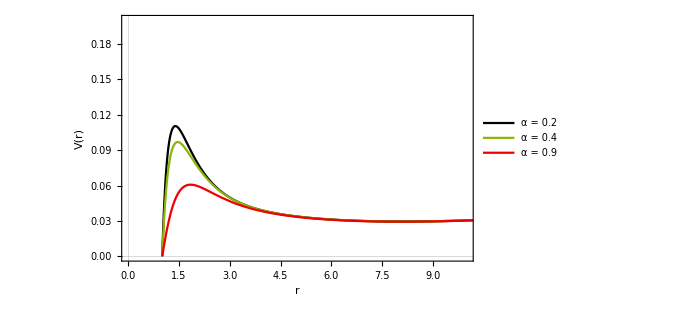

```mathematica
plotshowfunc[{0,10},{0,0.2}]
```

```mathematica
plotletafunc[ain_,letalist3values_,lambdain_,horpos_,vertpos_]:=Block[{ε=1,a=ain},
times=50;
(**)
Block[{leta=letalist3values[[1]]},
 V1=Plot[{Veff[r,lambdain]},{r,-10*leta,10*leta},PlotRange->All,PlotTheme->"Scientific",PlotLegends->{Placed[{Style[(*"ℓ_η=0.5"*)StringTemplate["ℓ_η = ``"][letalist3values[[1]]],15]},{0.71,0.8}]},PlotStyle->colorlist[[1]],Frame->True];
];
(**)
Block[{leta=letalist3values[[2]]},
 V2=Plot[{Veff[r,lambdain]},{r,-10*leta,10*leta},PlotRange->All,PlotTheme->"Scientific",PlotLegends->{Placed[{Style[(*"ℓ_η=0.5"*)StringTemplate["ℓ_η = ``"][letalist3values[[2]]],15]},{0.71,0.7}]},PlotStyle->colorlist[[2]],Frame->True];
];
(**)
Block[{leta=letalist3values[[3]]},
 V3=Plot[{Veff[r,lambdain]},{r,-10*leta,10*leta},PlotRange->All,PlotTheme->"Scientific",PlotLegends->{Placed[{Style[(*"ℓ_η=0.5"*)StringTemplate["ℓ_η = ``"][letalist3values[[3]]],15]},{0.71,0.6}]},PlotStyle->colorlist[[3]],Frame->True];
];
];
```

Example

```mathematica
plotletafunc[0.5,{3,5,10},0]
```

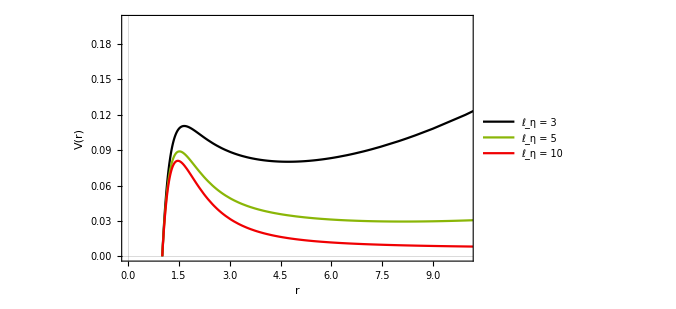

```mathematica
plotshowfunc[{0,10},{0,0.2}]
```

```mathematica
Options[PlotLegends]
```

{}

## Colors for plots

```mathematica
CD3 = ColorData[3,"ColorList"];
colorlist= CD3[[#]]& /@{1,4,6,3};
newred=ColorData[16,"ColorList"][[9]];
colorlist =  Insert[colorlist,newred,3]//Append[ColorData[14,"ColorList"][[2]]]
```

{RGBColor[0., 0., 0.],RGBColor[0.5411764705882353, 0.7137254901960784, 0.027450980392156862],RGBColor[0.9411764705882353, 0., 0.00784313725490196],RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824],RGBColor[0.996078431372549, 0.9882352941176471, 0.03529411764705882],RGBColor[0.9490196078431372, 0.29411764705882354, 0.050980392156862744]}

```mathematica
{RGBColor[0., 0., 0.],RGBColor[0.5411764705882353, 0.7137254901960784, 0.027450980392156862],RGBColor[0.9411764705882353, 0., 0.00784313725490196],RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824],RGBColor[0.996078431372549, 0.9882352941176471, 0.03529411764705882]}
```

```mathematica
ColorData[#,"ColorList"]& /@ Range[13,20]
```

{{RGBColor[0.6588235294117647, 0.4980392156862745, 0.49019607843137253],RGBColor[0.7215686274509804, 0.1843137254901961, 0.050980392156862744],RGBColor[0.803921568627451, 0.5450980392156862, 0.4588235294117647],RGBColor[0.8156862745098039, 0.6901960784313725, 0.6313725490196078],RGBColor[0.9490196078431372, 0.8745098039215686, 0.7176470588235294],RGBColor[0.3803921568627451, 0.3843137254901961, 0.6352941176470588],RGBColor[0.23137254901960785, 0.20784313725490197, 0.5529411764705883],RGBColor[0.5843137254901961, 0.5607843137254902, 0.6627450980392157],RGBColor[0.4666666666666667, 0.27450980392156865, 0.34901960784313724],RGBColor[0.596078431372549, 0.27450980392156865, 0.36470588235294116]},{RGBColor[0.8352941176470589, 0.5764705882352941, 0.5607843137254902],RGBColor[0.9490196078431372, 0.29411764705882354, 0.050980392156862744],RGBColor[1., 0.7333333333333333, 0.2],RGBColor[0.996078431372549, 0.9490196078431372, 0.44313725490196076],RGBColor[0.7058823529411765, 0.6862745098039216, 0.30196078431372547],RGBColor[0.41568627450980394, 0.5450980392156862, 0.12156862745098039],RGBColor[0.0196078431372549, 0.20784313725490197, 0.4627450980392157],RGBColor[0.6862745098039216, 0.7215686274509804, 0.8117647058823529],RGBColor[0.42745098039215684, 0.06666666666666667, 0.1568627450980392],RGBColor[0.8549019607843137, 0.19607843137254902, 0.27450980392156865]},{RGBColor[0.40784313725490196, 0.15294117647058825, 0.13725490196078433],RGBColor[0.6588235294117647, 0.5607843137254902, 0.5333333333333333],RGBColor[0.8313725490196079, 0.43529411764705883, 0.12941176470588237],RGBColor[0.8941176470588236, 0.8274509803921568, 0.7647058823529411],RGBColor[0.9372549019607843, 0.7764705882352941, 0.3137254901960784],RGBColor[0.23921568627450981, 0.27058823529411763, 0.4627450980392157],RGBColor[0.23529411764705882, 0.1450980392156863, 0.4588235294117647],RGBColor[0.36470588235294116, 0.23921568627450981, 0.43137254901960786],RGBColor[0.2196078431372549, 0.12549019607843137, 0.18823529411764706],RGBColor[0.5529411764705883, 0.12941176470588237, 0.2235294117647059],RGBColor[0.7058823529411765, 0.2627450980392157, 0.27058823529411763]},{RGBColor[0.4549019607843137, 0.050980392156862744, 0.023529411764705882],RGBColor[0.6784313725490196, 0.3137254901960784, 0.],RGBColor[0.9058823529411765, 0.6392156862745098, 0.07058823529411765],RGBColor[0.16470588235294117, 0.41568627450980394, 0.11764705882352941],RGBColor[0.8549019607843137, 0.9607843137254902, 1.],RGBColor[0.12156862745098039, 0.5098039215686274, 0.7333333333333333],RGBColor[0.6392156862745098, 0.5607843137254902, 0.7529411764705882],RGBColor[0.1450980392156863, 0.11372549019607843, 0.16470588235294117],RGBColor[0.9411764705882353, 0., 0.00784313725490196]},{RGBColor[0.2823529411764706, 0.22745098039215686, 0.2235294117647059],RGBColor[0.5647058823529412, 0.23137254901960785, 0.15294117647058825],RGBColor[0.6392156862745098, 0.39215686274509803, 0.3333333333333333],RGBColor[0.8627450980392157, 0.6196078431372549, 0.2627450980392157],RGBColor[0.9647058823529412, 0.788235294117647, 0.5254901960784314],RGBColor[0.4588235294117647, 0.592156862745098, 0.4627450980392157],RGBColor[0.23921568627450981, 0.45098039215686275, 0.24705882352941178],RGBColor[0.34509803921568627, 0.5803921568627451, 0.6901960784313725],RGBColor[0.1843137254901961, 0.39215686274509803, 0.49019607843137253],RGBColor[0.5686274509803921, 0.7490196078431373, 0.8431372549019608]},{RGBColor[0.7647058823529411, 0.5568627450980392, 0.5411764705882353],RGBColor[0.9921568627450981, 0.788235294117647, 0.7568627450980392],RGBColor[0.29411764705882354, 0.19215686274509805, 0.10588235294117647],RGBColor[0.37254901960784315, 0.2784313725490196, 0.19215686274509805],RGBColor[0.29411764705882354, 0.27058823529411763, 0.18823529411764706],RGBColor[0.7098039215686275, 0.6980392156862745, 0.5058823529411764],RGBColor[0.8705882352941177, 0.8784313725490196, 0.6901960784313725],RGBColor[0.27058823529411763, 0.33725490196078434, 0.28627450980392155],RGBColor[0.6980392156862745, 0.43529411764705883, 0.4470588235294118]},{RGBColor[0.5686274509803921, 0.043137254901960784, 0.],RGBColor[0.5607843137254902, 0.22745098039215686, 0.2],RGBColor[0.6627450980392157, 0.3333333333333333, 0.],RGBColor[0.8470588235294118, 0.6392156862745098, 0.42745098039215684],RGBColor[0.7686274509803922, 0.4627450980392157, 0.14901960784313725],RGBColor[0.01568627450980392, 0.19215686274509805, 0.09803921568627451],RGBColor[0.19215686274509805, 0.3686274509803922, 0.27450980392156865],RGBColor[0.4, 0.5254901960784314, 0.4588235294117647],RGBColor[0.06666666666666667, 0.15294117647058825, 0.20784313725490197]},{RGBColor[0.7450980392156863, 0.06666666666666667, 0.00392156862745098],RGBColor[0.9019607843137255, 0.19607843137254902, 0.12941176470588237],RGBColor[0.3568627450980392, 0.054901960784313725, 0.01568627450980392],RGBColor[0.6823529411764706, 0.41568627450980394, 0.],RGBColor[0.8352941176470589, 0.6274509803921569, 0.08627450980392157],RGBColor[0.9803921568627451, 0.7803921568627451, 0.25882352941176473],RGBColor[1., 0.9058823529411765, 0.6549019607843137],RGBColor[0.3843137254901961, 0.6, 0.8784313725490196],RGBColor[0.06274509803921569, 0.25882352941176473, 0.5137254901960784],RGBColor[0.12549019607843137, 0.36470588235294116, 0.6784313725490196]}}

## Definitions

## Metric & V_eff definitions

```mathematica
(* mass fixed such r_horizon = 1 *)
m=0.1;(*(√(1+a^2) (1+a^2+9 leta^2))/(24 leta^2)+1/8 leta ArcTan[(√(1+a^2))/leta]/.a->0;*)
```

```mathematica
(*metric*) 
F[x_]:=SetPrecision[(3 -(8 m)/x+x^2/(3 leta^2)+leta/x ArcTan[x/leta]),20];
(*I dont include the minus sign on the gtt definition *)
gtt[x_]:=SetPrecision[ 1/4 F[√(x^2+a^2)],20];
grr[x_]:= SetPrecision[((x^2+a^2+2 leta^2)^2)/((x^2+a^2+leta^2)^2 F[√(x^2+a^2)]),20];
(**)
gθθ[x_]:=SetPrecision[x^2+a^2,20];
p[x_]:=SetPrecision[ √gθθ[x],20];
PsiSquare[x_]:=SetPrecision[-ε/(8 π leta^2)*(x^2 grr[x])/(x^2+leta^2),20];
(*useful definitions (for "easier" calculations) *)
(*h[x_]:=SetPrecision[√(gtt[x]/grr[x]),20];*)
(* η=-leta^2/ε;*)

(*potential*)
Veff[x_,lam_]:= Evaluate[SetPrecision[gtt[x]/p[x]^2 lam(lam+1)+1/(2 grr[x]^2 p[x])( 2 gtt[x] grr [x] D[p[x],{x,2}]+grr[x]  D[gtt[x],x]  D[p[x],x] -gtt[x] D[grr[x],x]   D[p[x],x] )  ,100]] ;
```

```mathematica
horizonsol[letain_,ain_]:=
NumberForm[NSolve[3 -(8 m)/(√(r^2+ain^2))+(r^2+ain^2)/(3 letain^2)+letain/(√(r^2+ain^2))ArcTan[(√(r^2+ain^2))/letain]==0,r,Reals],200][[1,2,1,2]]
```

```mathematica
horizonsol[#,1]&/@{1,2,5,10}
```

{1.41903,1.67057,1.72941,1.73187}

```mathematica
horizonsol[50,#]&/@{1.9,2,2.5}
horizonsol[10,#]&/@{1.9,2,2.5}
horizonsol[5,#]&/@{1.9,2,2.5}
horizonsol[1,#]&/@{1.7,1.8}
```

Part::partw: Part 2 of {} does not exist.

{0.624499,{}⟦1,2,1,2⟧,{}⟦1,2,1,2⟧}

Part::partw: Part 2 of {} does not exist.

{0.624002,{}⟦1,2,1,2⟧,{}⟦1,2,1,2⟧}

Part::partw: Part 2 of {} does not exist.

{0.617136,{}⟦1,2,1,2⟧,{}⟦1,2,1,2⟧}

Part::partw: Part 2 of {} does not exist.

```mathematica
horizonsol[2,#]&/@{2,3,5,10}
horizonsol[#,2]&/@{2,5,10,50}
```

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{{}⟦1,2,1,2⟧,{}⟦1,2,1,2⟧,{}⟦1,2,1,2⟧,{}⟦1,2,1,2⟧}

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{{}⟦1,2,1,2⟧,{}⟦1,2,1,2⟧,{}⟦1,2,1,2⟧,{}⟦1,2,1,2⟧}

```mathematica
horizonsol[5,#]&/@{1,2,3,5,10}
```

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{{}⟦1,2,1,2⟧,{}⟦1,2,1,2⟧,{}⟦1,2,1,2⟧,{}⟦1,2,1,2⟧,{}⟦1,2,1,2⟧}

```mathematica
horizonsol[1]
```

0.763543

```mathematica
horizonsolmass[massin_,letain_,ain_]:=
NumberForm[NSolve[3 -(8 massin)/(√(r^2+ain^2))+(r^2+ain^2)/(3 letain^2)+letain/(√(r^2+ain^2))ArcTan[(√(r^2+ain^2))/letain]==0,r,Reals],200](*[[1,2,1,2]]*)
```

```mathematica
horizonsolmass[#,1,0.6]&/@{0.1,0.2,0.3,0.4}
```

{{},{},{},{{r→-0.5128326929564404},{r→0.5128326929564404}}}

## tortoise

```mathematica
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
leta=2;a=0.6;ε=1; m=0.3;
(**)
Print["Horizon = ",horizonsol[leta,a]]
x= First[x1/. NDSolve[{x1'[xstar]==((1/4(3 -(8 m)/(√(x1[xstar]^2+a^2))+(x1[xstar]^2+a^2)/(3 leta^2)+leta/(√(x1[xstar]^2+a^2))ArcTan[(√(x1[xstar]^2+a^2))/leta]))/(((x1[xstar]^2+a^2+2 leta^2)^2)/((x1[xstar]^2+a^2+leta^2)^2)(1/(3 -(8 m)/(√(x1[xstar]^2+a^2))+(x1[xstar]^2+a^2)/(3 leta^2)+leta/(√(x1[xstar]^2+a^2))ArcTan[(√(x1[xstar]^2+a^2))/leta]))) )^(1/2),x1[0]==0.00001(*SetPrecision[1.01*horizonsol[leta,a],200]*)(*throat @ x=0SetPrecision[1.01*horizonsol[leta,a],200]*)},
x1,{xstar,-10000,10000},Method->Automatic,
MaxSteps->10^7,
WorkingPrecision->100,
AccuracyGoal->50,
PrecisionGoal->20,
InterpolationOrder->All]]
{xstarmin,xstarmax}=InterpolatingFunctionDomain[x][[1]]
x[#]& /@{xstarmin,xstarmax}
```

Part::partw: Part 2 of {} does not exist.

Horizon = {}⟦1,2,1,2⟧

NDSolve::precw: The precision of the differential equation ({{x1'[xstar]==1/2 √((Plus[«2»]^2 Plus[«4»]^2)/Plus[«2»]^2),x1[0]==0.00001},{},{},{},{}}) is less than WorkingPrecision (100.).

NDSolve::ndsz: At xstar == -72.85057655103200074284087274276289404864069261848915416861532819114002922554309073748992608722936187, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At xstar == 72.80020560167911337612531215984821348582585556751925576836874842519950000141502183298859323467001081, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction[{{-72.85057655103200074284087274276289404864069261848915416861532819114002922554309073748992608722936187, 72.80020560167911337612531215984821348582585556751925576836874842519950000141502183298859323467001081}}, <>]

{-72.85057655103200074284087274276289404864069261848915416861532819114002922554309073748992608722936187,72.80020560167911337612531215984821348582585556751925576836874842519950000141502183298859323467001081}

{-7.×10^86,9.×10^86}

## Further checking r_*vs V_eff

### General

Now we just check the general behavior of the r(r_*) function and how it may affect the V_eff

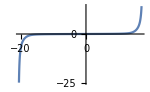
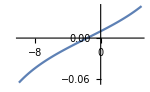

```mathematica
(*r[rstar_]=r[rstar]/.First[Out[12]];*)
Row[{Plot[{x[xstar]},{xstar,-20.5,17},PlotRange->Full,ImageSize->150],
Plot[{x[xstar]},{xstar,-10,5},PlotRange->All,ImageSize->150]}]
```

a = 1

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Plot::plln: Limiting value {}⟦1,2,1,2⟧ in {r,{}⟦1,2,1,2⟧,10} is not a machine-sized real number.

General::stop: Further output of Plot::plln will be suppressed during this calculation.

Show::gtype: Plot is not a type of graphics.

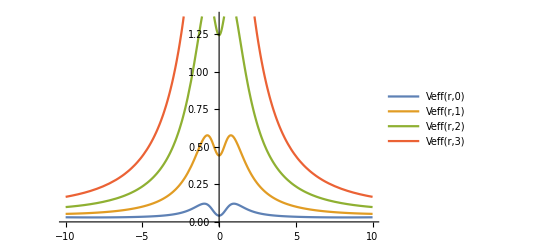

```mathematica
Block[{m=0.4,leta=5,a=1,ε=1 },
(*Print["Horizon = ",horizonsol[leta,a]];*)
Print["a = ",a];
VrPlot=Plot[{Veff[r,0],Veff[r,1],Veff[r,2],Veff[r,3]},{r,horizonsol[leta,a],10},PlotRange->Automatic(*{{horizon,10*horizon},{0,100}}*),AxesOrigin->{0,0},PlotLegends->"Expressions"];
VrPlot2=Plot[{Veff[r,0],Veff[r,1],Veff[r,2],Veff[r,3]},{r,-10,10},PlotRange->Automatic(*{{horizon,10*horizon},{0,100}}*),AxesOrigin->{0,0},PlotLegends->"Expressions"];
Show[VrPlot];
Show[VrPlot2]
]
```

### Plots !

Now wrt to r coordinate

```mathematica
plotleta[letain_,ain_,lamlist_,horpos_,verpos_]:=
Block[{leta=letain,a=ain},
Print["Horizon = ",horizonsol[leta,a]];
legendstyle={Style[StringTemplate["ℓ = ``"][lamlist[[1]]],15],Style[StringTemplate["ℓ = ``"][lamlist[[2]]],15],Style[StringTemplate["ℓ = ``"][lamlist[[3]]],15]};
VstarPlot=Plot[{Veff[r,lamlist[[1]]],Veff[r,lamlist[[2]]],Veff[r,lamlist[[3]]]},{r,-100,100},PlotRange->All,PlotTheme->"Scientific" ,PlotStyle->colorlist ,PlotLegends->{ Placed[legendstyle,{horpos,verpos}]},
ImageSize->500];
]
```

Horizon = horizonsol[1,0.6]

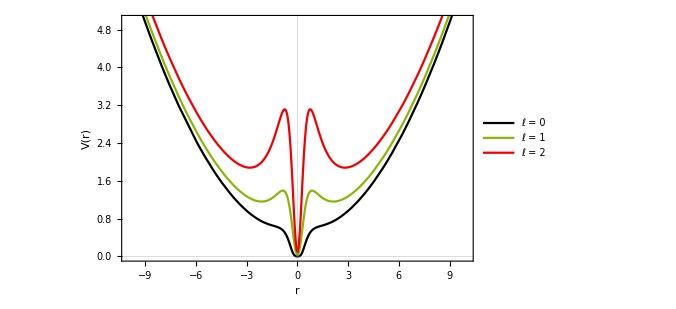

```mathematica
m=0.3;
plotleta[1,0.6,{0,1,2},.7,.7];
Show[VstarPlot, PlotRange->{{-10,10},{0,5}},
FrameLabel->{{HoldForm["V(r)" ],None},{HoldForm["r"],None}},
FrameStyle->Directive[Black,17],LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15},Background->White]
```

Part::partw: Part 2 of {} does not exist.

Horizon = {}⟦1,2,1,2⟧

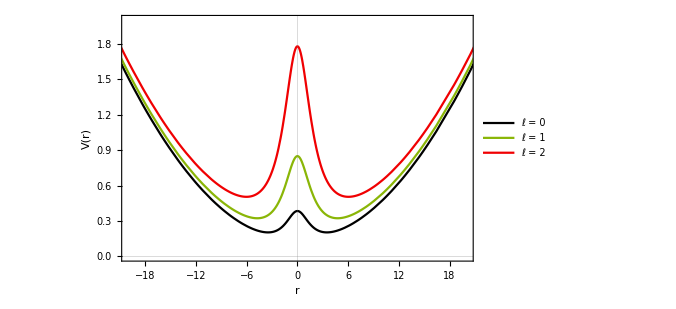

```mathematica
plotleta[2,2,{0,1,2},.7,.7];
Show[VstarPlot, PlotRange->{{-20,20},{0,2.}},
FrameLabel->{{HoldForm["V(r)" ],None},{HoldForm["r"],None}},
FrameStyle->Directive[Black,17],LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15},Background->White]
```

Part::partw: Part 2 of {} does not exist.

Horizon = {}⟦1,2,1,2⟧

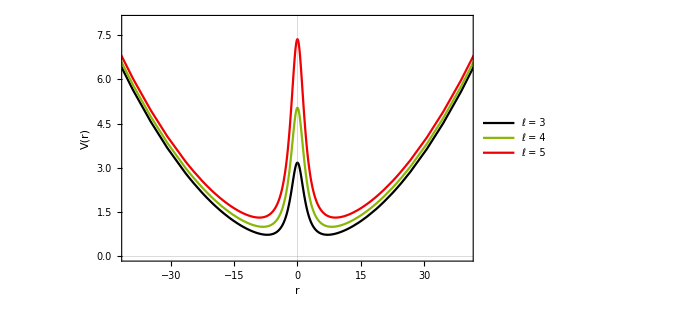

```mathematica
plotleta[2,2,{3,4,5},.85,.25];
Show[VstarPlot, PlotRange->{{-40,40},{0,8}},
FrameLabel->{{HoldForm["V(r)" ],None},{HoldForm["r"],None}},
FrameStyle->Directive[Black,17],LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15},Background->White]
```

```mathematica
plotleta[5,2,{0,1,2},.8,.55];
Show[VstarPlot, PlotRange->{{-90,90},{0,1.7}},
FrameLabel->{{HoldForm["V(r)" ],None},{HoldForm["r"],None}},
FrameStyle->Directive[Black,17],LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15},Background->White]
```

Part::partw: Part 2 of {} does not exist.

Horizon = {}⟦1,2,1,2⟧

Part::partw: Part 2 of {} does not exist.

Horizon = {}⟦1,2,1,2⟧

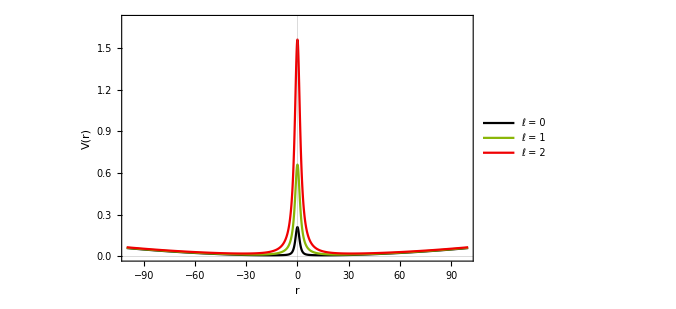

```mathematica
plotleta[10,2,{0,1,2},.8,.55];
Show[VstarPlot, PlotRange->{{-99,99},{0,1.7}},
FrameLabel->{{HoldForm["V(r)" ],None},{HoldForm["r"],None}},
FrameStyle->Directive[Black,17],LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15},Background->White]
```

```mathematica
Old code below , for plot insets
```

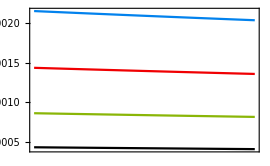

```mathematica
Block[{m=0.1,leta=100},plotinset=Plot[{{Veff[r,2],Veff[r,3],Veff[r,4],Veff[r,5]}},{r,1000*horizonsol[0.1,100],1050*horizonsol[0.1,100]},
PlotRange->Automatic,
PlotTheme->"Scientific",(*GridLines->{{etd,2 etd},None} ,GridLinesStyle->Directive[Black, Dashed,Thick],*)
PlotStyle->colorlist,Background->White,FrameStyle->Black,FrameTicks->{{True,False},{False,All}},
(*PlotLegends->{ Placed[LineLegend[{Style["l_η=0.8",15]}],{0.8,0.8}]},*)
ImageSize->270]
]
```

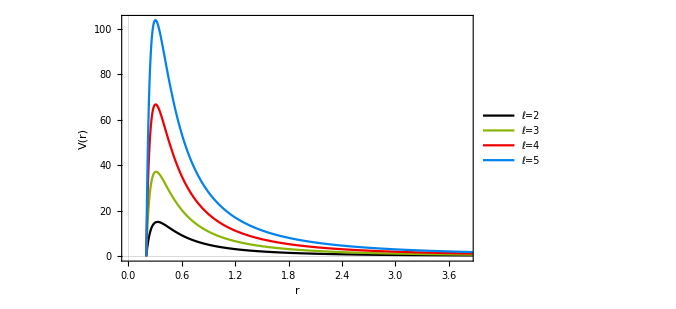

```mathematica
Block[{m=0.1,leta=100},
legendstyle={Style["ℓ=2",15],Style["ℓ=3",15],Style["ℓ=4",15],Style["ℓ=5",15]};
NewVstarPlot=Plot[{Veff[r,2],Veff[r,3],Veff[r,4],Veff[r,5]},{r,horizonsol[0.1,100],20*horizonsol[0.1,100]},PlotRange->All,PlotTheme->"Scientific" ,PlotStyle->colorlist ,PlotLegends->{ Placed[legendstyle,{0.3,0.66}]},
ImageSize->500,
Epilog-> {Inset[plotinset,{3.7,50},{210,0.0005},{65,60}]}];
]

Show[NewVstarPlot, PlotRange->{{0,3.8},Automatic},
FrameLabel->{{HoldForm["V(r)" ],None},{HoldForm["r"],None}},
FrameStyle->Directive[Black,17],LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15},Background->White]
```

## Finite Difference Code

### FD - Code

Finite Difference - Implementation CODE

```mathematica
FDrin[start_,stop_,iter_,tfinal_,lam_]:=(
Clear[ψ,Length1,Δrstar,Δt,imax,imin,lambda,Adis,Bdis,jmax,σ,center,ψinit2,ψinit,V,ψinit3,ψbound,ψbound2];

(*Discretization setup*)
(*rstarmax=stop; rstarmin=start;*) Length1=stop-start;
 Δrstar=Length1/iter; Δt=Δrstar*0.8;
imax=IntegerPart[N[stop/Δrstar]];imin=IntegerPart[N[start/Δrstar]];
jmax = IntegerPart[N[tfinal/Δt]];
(**)
lambda=lam;
(*-------messages to check code behavior-------*)
printstyle={Blue,14,Italic,FontFamily->"Courier"};
Print["leta = ",leta,", m = ",m ,", a = ",a, ", lambda = ",lambda];
Print["r_horizon = ",horizonsol[leta,a]];
Print[Style["Location of Gaussian's center = ",Blue,14,Italic,FontFamily->"Courier"],Style[x[0],Blue,14,Italic,FontFamily->"Courier"]];
(**)
Print[Style["# of Iterations in space = ",printstyle],Style[iter,14,Blue,Italic]];
(**)
Print[ Style["(r_*)^max =  ",printstyle],Style[stop " , ",printstyle],
Style["r^max =  ",printstyle], Style[NumberForm[ x[stop],20],printstyle]];
Print[ Style["(r_*)^min =  ",printstyle],Style[start " , ",printstyle],
Style[" r^min =  ",printstyle], Style[NumberForm[ x[start],20],printstyle]];
(**)
Print[Style[ "I_max = ",printstyle],Style[imax,printstyle]];
Print[Style[ "I_min = ",printstyle],Style[imin,printstyle]];
(**)
Print[Style["Space Discretization step = ",printstyle],Style[N[Δrstar],printstyle]];
Print[Style["t_final/M = ",printstyle],Style[N[tfinal/m],printstyle]];
Print[Style[ "# of Iterations in time = J_max = ",printstyle],Style[jmax,printstyle]];
Print[Style["Time Discretization step = ",printstyle],Style[Δt,printstyle]];
Print[Style["Δt/(Δr_*) = ",printstyle],Style[N[Δt/Δrstar],printstyle]];(*--V effective & functions A(r)/B(r)Discretization--*)
(*Do[V[i]=Veff[r[i*Δrstar],lam],{i,imin,imax}];
Do[Adis[i]=A[r[i*Δrstar]],{i,imin,imax}];
Do[Bdis[i]=B[r[i*Δrstar]],{i,imin,imax}];*)
(*interVeff=Interpolation[Table[{rstar,Veff[r[rstar],lam]},{rstar,-1000,rstarmax,0.1}],InterpolationOrder->3];*)

V[i_]:=V[i]=(*interVeff[i*Δrstar]*)SetPrecision[ Veff[x[i*Δrstar],lam],100];

(*--------Initial Condtions--------*) 
σ=0.1;center=0;
ψ[i_,0]:=ψinit2[rstar] /.rstar->i Δrstar  ;
ψinit2[rstar_]:=SetPrecision[1/10 Exp[-(rstar-center)^2/(2 σ^2)],100];
ψ[i_,-1]:=ψinit[x[rstar]]  /.rstar->i Δrstar ;
ψinit[x[rstar_]]=0; 
(*-------Boundary Condition(s)-------*)
ψ[imax,j_]:=ψ[imax,j]= 0;
ψ[imin,j_]:=ψ[imin,j]= 0;(*comment out when ther is a horizon*)
(*--------Iterating Scheme---------*)

(*SetPrecision[ψ[imax-1,j-1]+(((Adis[imax-1] Bdis[imax-1]+Adis[imax] Bdis[imax])/2 Δt-Δrstar)/((Adis[imax-1] Bdis[imax-1]+Adis[imax] Bdis[imax])/2 Δt+Δrstar))*( ψ[imax-1,j]-ψ[imax,j-1]),40];*)ψ[i_,j_]:=ψ[i,j]=SetPrecision[ -ψ[i,j-2]+(Δt/Δrstar)^2(ψ[i+1,j-1]+ψ[i-1,j-1]) + (2-2 (Δt/Δrstar)^2-V[i] Δt^2) ψ[i,j-1] ,100] ;);
```

## Numerical Results - simulations

## Setup - leta = 2

### a = 2 - lambda = 0,1, 2

```mathematica
FDrin[xstarmin+10^-7,xstarmax-10^-7,1000,50,1]
```

leta = 2, m = 0.1, lambda = 1

Part::partw: Part 2 of {} does not exist.

r_horizon = {}⟦1,2,1,2⟧

Location of Gaussian's center = 0.01000000000000000020816681711721685132943093776702880859375

# of Iterations in space = 1000

(r_*)^max =  6.5188019782356927230231882024510029158389201645929019949558445754543690348213409868128929460742591  , r^max =  2.3999999999999994990×10^8

(r_*)^min =  -6.53493647576474314988240969198773972680739129086475185670261890856420915781985580322412301971006546  ,  r^min =  -2.3999999999999994991×10^8

I_max = 499

I_min = -500

Space Discretization step = 0.0130537

t_final/M = 500.

# of Iterations in time = J_max = 5471

Time Discretization step = 0.00913762

Δt/(Δr_*) = 0.7

```mathematica
Clear[Viplot,OrigV,VrPlot]
Viplot = ListPlot[Table[{i Δrstar,V[i]},{i,imin,imax}],PlotStyle->Directive[Black,Thick],PlotRange->All];
OrigV = Plot[Veff[x[rstar],lambda],{rstar,imin*Δrstar,(imax-10)*Δrstar},PlotStyle->colorlist,PlotRange->All];
VrPlot=Plot[{Veff[r,2]},{r,horizonsol[leta,a],10*horizonsol[leta,a]},PlotRange->Automatic,PlotStyle->colorlist(*{{horizon,10*horizon},{0,100}}*),AxesOrigin->{0,0},PlotLegends->"Expressions"];
```

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Plot::plln: Limiting value {}⟦1,2,1,2⟧ in {r,{}⟦1,2,1,2⟧,10 {}⟦1,2,1,2⟧} is not a machine-sized real number.

```mathematica
Psiplot = Plot[PsiSquare[x[rstar]],{rstar,imin*Δrstar,imax*Δrstar},PlotStyle->colorlist[[2]],PlotRange->All];
Psirplot = Plot[PsiSquare[r],{r,horizonsol[leta,a],10*horizonsol[leta,a]},PlotStyle->colorlist[[2]],PlotRange->All];
```

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Plot::plln: Limiting value {}⟦1,2,1,2⟧ in {r,{}⟦1,2,1,2⟧,10 {}⟦1,2,1,2⟧} is not a machine-sized real number.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Plot::plln: Limiting value {}⟦1,2,1,2⟧ in {r,{}⟦1,2,1,2⟧,10 {}⟦1,2,1,2⟧} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[{Plot[{Veff[r,2]},{r,horizonsol[leta,a],10 horizonsol[leta,a]},PlotRange→Automatic,PlotStyle→colorlist,AxesOrigin→{0,0},PlotLegends→Expressions],Plot[PsiSquare[r],{r,horizonsol[leta,a],10 horizonsol[leta,a]},PlotStyle→colorlist⟦2⟧,PlotRange→All]},ImageSize→Small].

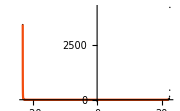
-Graphics-Show[{Plot[{Veff[r,2]},{r,horizonsol[leta,a],10 horizonsol[leta,a]},PlotRange→Automatic,PlotStyle→colorlist,AxesOrigin→{0,0},PlotLegends→Expressions],Plot[PsiSquare[r],{r,horizonsol[leta,a],10 horizonsol[leta,a]},PlotStyle→colorlist⟦2⟧,PlotRange→All]},ImageSize→Small]

```mathematica
Row[{Show[{Viplot,OrigV},PlotRange->Automatic(*{{-10,5},{-0.5,0.5}}*),ImageSize->Small], Show[{VrPlot,Psirplot},ImageSize->Small]}]
```

0.010000000000000000208

General::munfl: 1.01997 1.23414713047571214038746222179219347974135813193883436749719655359520345352609183514920750182825×10^-308 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.49 1.23421228525389385726070553292342729419329212093646053444624772024181268782785484438237466634774×10^-308 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.01997 9.04392172885406145617440667133635575852228728688806378342499959559380986297130784785327251461119×10^-311 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

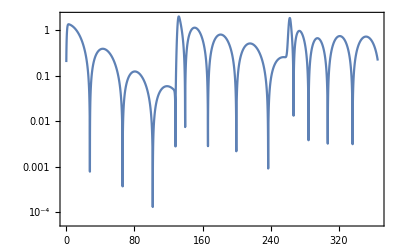

```mathematica
i=0;
(*lambda=5;*)
NumberForm[x[i*Δrstar],20]
Block[{$RecursionLimit=Infinity},ListLogPlot[{Table[{(j Δt)/m,Evaluate[Abs[ψ[i,j]]]},{j,4000}]  
(*,Table[{(j Δt)/M,Evaluate[10^3(j Δt)^(-(5))]},{j,1700,jmax}]*)},Joined->True,PlotRange->All,Frame->True] ]
```

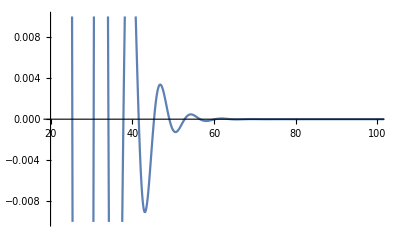

```mathematica
Block[{$RecursionLimit=Infinity},ListPlot[{Table[{(j Δt)/m,Evaluate[ψ[i,j]]},{j,0,3000}]  
(*,Table[{(j Δt)/M,Evaluate[10^3(j Δt)^(-(5))]},{j,1700,jmax}]*)},Joined->True,PlotRange->{{20,100},{-0.01,0.01}}] ]
```

```mathematica
data= Table[{(j Δt)/m ,ψ[i,j]},{j,0,4000}]  ;
SetDirectory["C:\\Users\\tsits\\OneDrive\\Έγγραφα\\Wolfram Mathematica\\PhD-2\\BhWhTransition\\Two_way_data\\"];
(*Export["GP_Rin_leta"<>ToString[leta]<>"m"<>ToString[m]<>"l"<>ToString[lambda]<>"data1.txt",data];*)
Print["m = ",m," , α = ",a," , leta = ",leta," , lambda = ",lambda];
Export["Two_way_leta"<>ToString[leta]<>"a"<>ToString[a]<>"m"<>ToString[m]<>"l"<>ToString[lambda]<>"data.txt",data,"Table","FieldSeparators"->" "];
(**)
Print["File name :"]
Print["Two_way_leta"<>ToString[leta]<>"a"<>ToString[a]<>"m"<>ToString[m]<>"l"<>ToString[lambda]<>"data.txt"]
```

m = 0.1 , α = 2 , leta = 2 , lambda = 1

File name :

Two_way_leta2a2m0.1l1data.txt

### Final graphs ✓

```mathematica
SetDirectory["C:\\Users\\tsits\\OneDrive\\Έγγραφα\\Wolfram Mathematica\\PhD-2\\BhWhTransition\\Two_way_data\\"];
data0=Import["Two_way_leta2a2m0.1l0data.txt","Table"]//ToExpression;
data1=Import["Two_way_leta2a2m0.1l1data.txt","Table"]//ToExpression;
data2=Import["Two_way_leta2a2m0.1l2data.txt","Table"]//ToExpression;
```

Below command : to read the number of lines a txt file has

```mathematica
null[_String]:=Null
Length@ReadList[#,null@String,NullRecords->True]&/@{"Two_way_leta2a2m0.1l0data.txt","Two_way_leta2a2m0.1l1data.txt","Two_way_leta2a2m0.1l2data.txt"}
```

{5001,4001}

```mathematica
data0[[;;,2]]=Abs[data0[[;;,2]]];
data1[[;;,2]]=Abs[data1[[;;,2]]];
data2[[;;,2]]=Abs[data2[[;;,2]]];
```

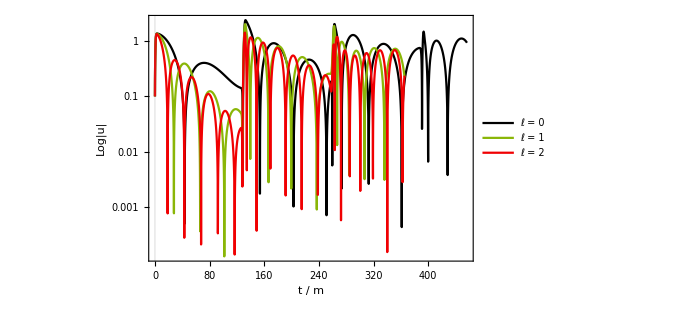

```mathematica
Block[{$RecursionLimit=Infinity,start=1},Show[ListLogPlot[{data0[[;;5000,;;]],data1[[;;4000,;;]],data2[[start;;4000,;;]]
},Joined->True,PlotRange->All,Frame->True,ImageSize->500,Background->White,PlotTheme->"Scientific",PlotLegends->Placed[{Style["ℓ = 0",15],Style["ℓ = 1",15],Style["ℓ = 2",15]},{Scaled[{0.8,0.05}], {0,0}}],PlotStyle->colorlist],FrameLabel-> {{RawBoxes[RowBox[{"Log|u|"}]],None},{"t / m",None}},
FrameStyle->Directive[Black,17],
PlotLabel->None,PlotRange->{{0,300},{1,-12}},
LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15}]]
```

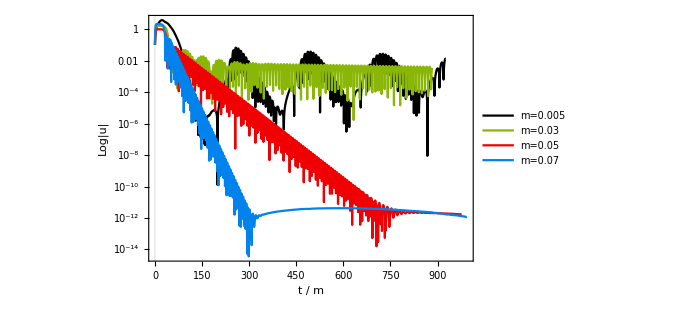

```mathematica
Block[{$RecursionLimit=Infinity,start=1},Show[ListLogPlot[{m0005data[[;;2000,;;]],m003data[[start;;3000,;;]],m005data[[start;;3000,;;]],m007data[[start;;8500,;;]]
},Joined->True,PlotRange->All,Frame->True,ImageSize->500,Background->White,PlotTheme->"Scientific",PlotLegends->Placed[LineLegend[{Style["m=0.005",15],Style["m=0.03",15],Style["m=0.05",15],Style["m=0.07",15],Style["m=0.1",15],Style["m=0.2",15]},LegendLayout->{"Row",1}],{Scaled[{0.1,0.85}], {0,0}}],PlotStyle->colorlist],FrameLabel-> {{RawBoxes[RowBox[{"Log|u|"}]],None},{"t / m",None}},
FrameStyle->Directive[Black,17],
PlotLabel->None,PlotRange->{{30,800},{2,-33}},
LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15}]]
```

```mathematica
SetDirectory["C:\\Users\\tsits\\OneDrive\\Έγγραφα\\Wolfram Mathematica\\PhD-2\\Grav_Petrurbations_NMDC\\3rd Run-Plots\\"];
Export["GP_Rin_leta01manymasses.pdf",NotebookRead[PreviousCell[]]]
```

GP_Rin_leta01manymasses.pdf

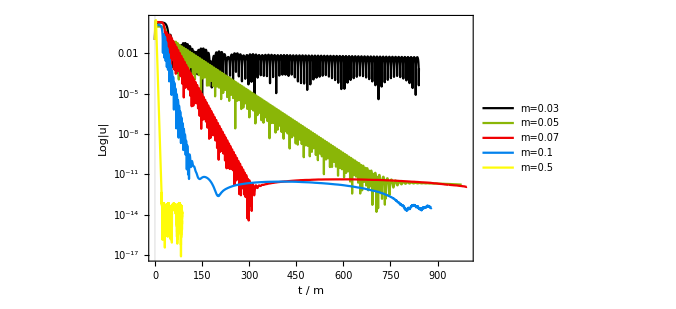

```mathematica
Block[{$RecursionLimit=Infinity,start=1},Show[ListLogPlot[{(*m0005data[[;;2000,;;]],m001data[[start;;2500,;;]],m00025data[[start;;3500,;;]],*)m003data[[start;;3500,;;]],(*m004data[[start;;3000,;;]],*)m005data[[start;;3000,;;]],m007data[[start;;8500,;;]],m01data[[start;;6000,;;]],m05data[[start;;5500,;;]](*,m07data[[start;;1500,;;]]*)
},Joined->True,PlotRange->All,Frame->True,ImageSize->500,Background->White,PlotTheme->"Scientific",PlotLegends->Placed[{(*Style["m=0.005",15],Style["m=0.01",15],Style["m=0.025",15],*)Style["m=0.03",15],(*Style["m=0.04",15],*)Style["m=0.05",15],Style["m=0.07",15],Style["m=0.1",15],Style["m=0.5",15],Style["m=0.7",15]},Right(*{Scaled[{0.01,0.01}], {0,0}}*)],PlotStyle->colorlist],FrameLabel-> {{RawBoxes[RowBox[{"Log|u|"}]],None},{"t / m",None}},
FrameStyle->Directive[Black,17],
PlotLabel->None,PlotRange->{{0,800},{0,-32}},
LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15}]]
```

```mathematica
SetDirectory["C:\\Users\\tsits\\OneDrive\\Έγγραφα\\Wolfram Mathematica\\PhD-2\\Grav_Petrurbations_NMDC\\3rd Run-Plots\\"];
Export["GP_Rin_leta01manymasses.pdf",NotebookRead[PreviousCell[]]]
```

GP_Rin_leta01manymasses.pdf

## Setup - leta = 5

### a = 2 - lambda = 0,1,2

```mathematica
FDrin[xstarmin+10^-7,xstarmax-10^-7,1000,50,0]
```

leta = 5, m = 0.1, lambda = 0

Part::partw: Part 2 of {} does not exist.

r_horizon = {}⟦1,2,1,2⟧

Location of Gaussian's center = 0.01000000000000000020816681711721685132943093776702880859375

# of Iterations in space = 1000

(r_*)^max =  17.4764373822183468142403104941055710990418011660397257898504328037197319732391995147997131713303514  , r^max =  1.4999999999999999541×10^9

(r_*)^min =  -17.497100617529015261811133320858110215303887903336511579245316994241647840584090618139811470372699  ,  r^min =  -1.4999999999999999541×10^9

I_max = 499

I_min = -500

Space Discretization step = 0.0349735

t_final/M = 500.

# of Iterations in time = J_max = 2042

Time Discretization step = 0.0244815

Δt/(Δr_*) = 0.7

```mathematica
Clear[Viplot,OrigV,VrPlot]
Viplot = ListPlot[Table[{i Δrstar,V[i]},{i,imin,imax}],PlotStyle->Directive[Black,Thick],PlotRange->All];
OrigV = Plot[Veff[x[rstar],lambda],{rstar,imin*Δrstar,(imax-10)*Δrstar},PlotStyle->colorlist,PlotRange->All];
VrPlot=Plot[{Veff[r,2]},{r,horizonsol[leta,a],10*horizonsol[leta,a]},PlotRange->Automatic,PlotStyle->colorlist(*{{horizon,10*horizon},{0,100}}*),AxesOrigin->{0,0},PlotLegends->"Expressions"];
```

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Plot::plln: Limiting value {}⟦1,2,1,2⟧ in {r,{}⟦1,2,1,2⟧,10 {}⟦1,2,1,2⟧} is not a machine-sized real number.

```mathematica
Psiplot = Plot[PsiSquare[x[rstar]],{rstar,imin*Δrstar,imax*Δrstar},PlotStyle->colorlist[[2]],PlotRange->All];
Psirplot = Plot[PsiSquare[r],{r,horizonsol[leta,a],10*horizonsol[leta,a]},PlotStyle->colorlist[[2]],PlotRange->All];
```

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Plot::plln: Limiting value {}⟦1,2,1,2⟧ in {r,{}⟦1,2,1,2⟧,10 {}⟦1,2,1,2⟧} is not a machine-sized real number.

```mathematica
Row[{Show[{Viplot,OrigV},PlotRange->Automatic(*{{-10,5},{-0.5,0.5}}*),ImageSize->Small], Show[{VrPlot,Psirplot},ImageSize->Small]}]
```

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Plot::plln: Limiting value {}⟦1,2,1,2⟧ in {r,{}⟦1,2,1,2⟧,10 {}⟦1,2,1,2⟧} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[{Plot[{Veff[r,2]},{r,horizonsol[leta,a],10 horizonsol[leta,a]},PlotRange→Automatic,PlotStyle→colorlist,AxesOrigin→{0,0},PlotLegends→Expressions],Plot[PsiSquare[r],{r,horizonsol[leta,a],10 horizonsol[leta,a]},PlotStyle→colorlist⟦2⟧,PlotRange→All]},ImageSize→Small].

-Graphics-Show[{Plot[{Veff[r,2]},{r,horizonsol[leta,a],10 horizonsol[leta,a]},PlotRange→Automatic,PlotStyle→colorlist,AxesOrigin→{0,0},PlotLegends→Expressions],Plot[PsiSquare[r],{r,horizonsol[leta,a],10 horizonsol[leta,a]},PlotStyle→colorlist⟦2⟧,PlotRange→All]},ImageSize→Small]

0.010000000000000000208

General::munfl: 1.01997 1.58606348055586141368368266350348430123263755450232365828885443890742237742731300314117282497263×10^-311 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.49 1.58606348056003027115727111876140985276032677034561872120657867701230517409460492740165414052311×10^-311 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.01997 2.73356330369904991295149095190492079889113555065907452749907027710123740964133216353898022584137×10^-317 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

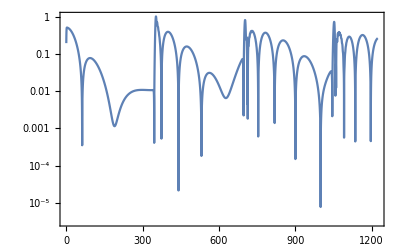

```mathematica
i=0;
(*lambda=5;*)
NumberForm[x[i*Δrstar],20]
Block[{$RecursionLimit=Infinity},ListLogPlot[{Table[{(j Δt)/m,Evaluate[Abs[ψ[i,j]]]},{j,5000}]  
(*,Table[{(j Δt)/M,Evaluate[10^3(j Δt)^(-(5))]},{j,1700,jmax}]*)},Joined->True,PlotRange->All,Frame->True] ]
```

```mathematica
Block[{$RecursionLimit=Infinity},ListPlot[{Table[{(j Δt)/m,Evaluate[ψ[i,j]]},{j,0,3000}]  
(*,Table[{(j Δt)/M,Evaluate[10^3(j Δt)^(-(5))]},{j,1700,jmax}]*)},Joined->True,PlotRange->{{20,100},{-0.01,0.01}}] ]
```

-Graphics-

```mathematica
data= Table[{(j Δt)/m ,ψ[i,j]},{j,0,5000}]  ;
SetDirectory["C:\\Users\\tsits\\OneDrive\\Έγγραφα\\Wolfram Mathematica\\PhD-2\\BhWhTransition\\Two_way_data\\"];
(**)
Print["m = ",m," , α = ",a," , leta = ",leta," , lambda = ",lambda];
Export["Two_way_leta"<>ToString[leta]<>"a"<>ToString[a]<>"m"<>ToString[m]<>"l"<>ToString[lambda]<>"data.txt",data,"Table","FieldSeparators"->" "];
(**)
Print["File name :"]
Print["Two_way_leta"<>ToString[leta]<>"a"<>ToString[a]<>"m"<>ToString[m]<>"l"<>ToString[lambda]<>"data.txt"]
```

m = 0.1 , α = 2 , leta = 5 , lambda = 0

File name :

Two_way_leta5a2m0.1l0data.txt

### Final graphs ✓

```mathematica
SetDirectory["C:\\Users\\tsits\\OneDrive\\Έγγραφα\\Wolfram Mathematica\\PhD-2\\BhWhTransition\\Two_way_data\\"];
data0=Import["Two_way_leta5a2m0.1l0data.txt","Table"]//ToExpression;
data1=Import["Two_way_leta5a2m0.1l1data.txt","Table"]//ToExpression;
data2=Import["Two_way_leta5a2m0.1l2data.txt","Table"]//ToExpression;(**)
```

Below command : to read the number of lines a txt file has

```mathematica
null[_String]:=Null
Length@ReadList[#,null@String,NullRecords->True]&/@{"Two_way_leta5a2m0.1l0data.txt","Two_way_leta5a2m0.1l1data.txt","Two_way_leta5a2m0.1l2data.txt"}
```

{5001,5001,5001}

```mathematica
data0[[;;,2]]=Abs[data0[[;;,2]]];
data1[[;;,2]]=Abs[data1[[;;,2]]];
data2[[;;,2]]=Abs[data2[[;;,2]]];
```

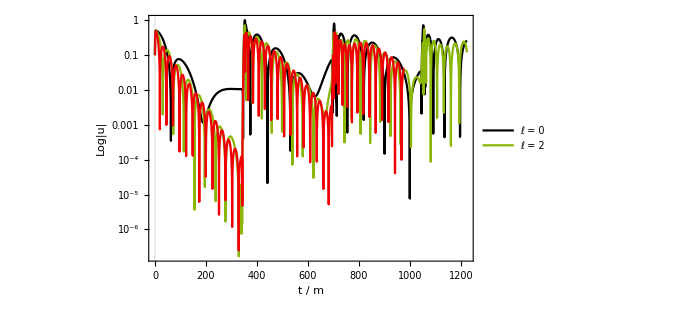

```mathematica
Block[{$RecursionLimit=Infinity,start=1},Show[ListLogPlot[{data0[[;;5000,;;]],data1[[;;5000,;;]],data2[[start;;4000,;;]]
},Joined->True,PlotRange->All,Frame->True,ImageSize->500,Background->White,PlotTheme->"Scientific",PlotLegends->Placed[{Style["ℓ = 0",15],Style["ℓ = 2",15]},{Scaled[{0.8,0.1}], {0,0}}],PlotStyle->colorlist],FrameLabel-> {{RawBoxes[RowBox[{"Log|u|"}]],None},{"t / m",None}},
FrameStyle->Directive[Black,17],
PlotLabel->None,PlotRange->{{0,800},{1,-18}},
LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15}]]
```

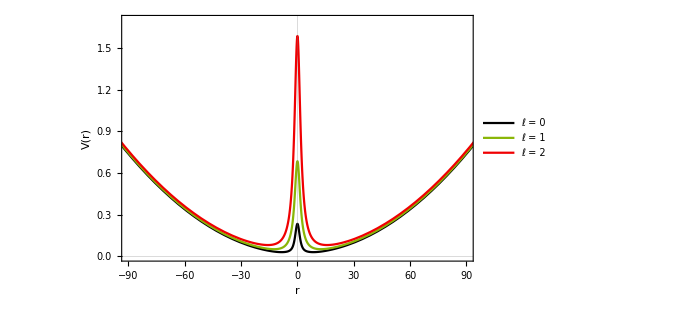

```mathematica
SetDirectory["C:\\Users\\tsits\\OneDrive\\Έγγραφα\\Wolfram Mathematica\\PhD-2\\Grav_Petrurbations_NMDC\\3rd Run-Plots\\"];
Export["GP_Rin_leta01manymasses.pdf",NotebookRead[PreviousCell[]]]
```

GP_Rin_leta01manymasses.pdf

## Setup - leta = 10

### a = 2 - lambda = 0, 1, 2

```mathematica
FDrin[xstarmin+10^-7,xstarmax-10^-7,2000,50,2]
```

leta = 10, m = 0.1, lambda = 2

Part::partw: Part 2 of {} does not exist.

r_horizon = {}⟦1,2,1,2⟧

Location of Gaussian's center = 0.01000000000000000020816681711721685132943093776702880859375

# of Iterations in space = 2000

(r_*)^max =  35.2171734372073154524777770579329861365976433032112434144529655328873848010506516144823204868495684  , r^max =  5.9999999999999999528×10^9

(r_*)^min =  -35.2389664119842477776947450160952698262770151672855688027846841812034531415941957645872061948362467  ,  r^min =  -5.9999999999999999529×10^9

I_max = 999

I_min = -1000

Space Discretization step = 0.0352281

t_final/M = 500.

# of Iterations in time = J_max = 2027

Time Discretization step = 0.0246596

Δt/(Δr_*) = 0.7

```mathematica
Clear[Viplot,OrigV,VrPlot]
Viplot = ListPlot[Table[{i Δrstar,V[i]},{i,imin,imax}],PlotStyle->Directive[Black,Thick],PlotRange->All];
OrigV = Plot[Veff[x[rstar],lambda],{rstar,imin*Δrstar,(imax-10)*Δrstar},PlotStyle->colorlist,PlotRange->All];
VrPlot=Plot[{Veff[r,2]},{r,horizonsol[leta,a],10*horizonsol[leta,a]},PlotRange->Automatic,PlotStyle->colorlist(*{{horizon,10*horizon},{0,100}}*),AxesOrigin->{0,0},PlotLegends->"Expressions"];
```

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Plot::plln: Limiting value {}⟦1,2,1,2⟧ in {r,{}⟦1,2,1,2⟧,10 {}⟦1,2,1,2⟧} is not a machine-sized real number.

```mathematica
Psiplot = Plot[PsiSquare[x[rstar]],{rstar,imin*Δrstar,imax*Δrstar},PlotStyle->colorlist[[2]],PlotRange->All];
Psirplot = Plot[PsiSquare[r],{r,horizonsol[leta,a],10*horizonsol[leta,a]},PlotStyle->colorlist[[2]],PlotRange->All];
```

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Plot::plln: Limiting value {}⟦1,2,1,2⟧ in {r,{}⟦1,2,1,2⟧,10 {}⟦1,2,1,2⟧} is not a machine-sized real number.

```mathematica
Row[{Show[{Viplot,OrigV},PlotRange->Automatic(*{{-10,5},{-0.5,0.5}}*),ImageSize->Small], Show[{VrPlot,Psirplot},ImageSize->Small]}]
```

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Plot::plln: Limiting value {}⟦1,2,1,2⟧ in {r,{}⟦1,2,1,2⟧,10 {}⟦1,2,1,2⟧} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[{Plot[{Veff[r,2]},{r,horizonsol[leta,a],10 horizonsol[leta,a]},PlotRange→Automatic,PlotStyle→colorlist,AxesOrigin→{0,0},PlotLegends→Expressions],Plot[PsiSquare[r],{r,horizonsol[leta,a],10 horizonsol[leta,a]},PlotStyle→colorlist⟦2⟧,PlotRange→All]},ImageSize→Small].

-Graphics-Show[{Plot[{Veff[r,2]},{r,horizonsol[leta,a],10 horizonsol[leta,a]},PlotRange→Automatic,PlotStyle→colorlist,AxesOrigin→{0,0},PlotLegends→Expressions],Plot[PsiSquare[r],{r,horizonsol[leta,a],10 horizonsol[leta,a]},PlotStyle→colorlist⟦2⟧,PlotRange→All]},ImageSize→Small]

0.010000000000000000208

General::munfl: 1.01978 2.9407458957224286130932874357836512760225849423932950124673897484878506363758492865467617205351×10^-310 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.49 2.94074589572913941935440908649399726144535283375040796660716125180036966356962305176092803598688×10^-310 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.01979 4.72676966964443953282591525370511657854887083867074810287624858883003018922167070850092431063261×10^-316 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

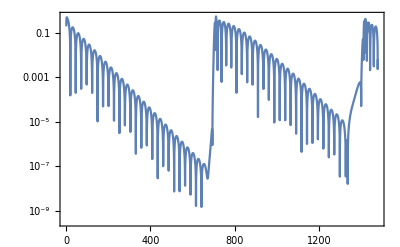

```mathematica
i=0;
(*lambda=5;*)
NumberForm[x[i*Δrstar],20]
Block[{$RecursionLimit=Infinity},ListLogPlot[{Table[{(j Δt)/m,Evaluate[Abs[ψ[i,j]]]},{j,6000}]  
(*,Table[{(j Δt)/M,Evaluate[10^3(j Δt)^(-(5))]},{j,1700,jmax}]*)},Joined->True,PlotRange->All,Frame->True] ]
```

```mathematica
Block[{$RecursionLimit=Infinity},ListPlot[{Table[{(j Δt)/m,Evaluate[ψ[i,j]]},{j,0,3000}]  
(*,Table[{(j Δt)/M,Evaluate[10^3(j Δt)^(-(5))]},{j,1700,jmax}]*)},Joined->True,PlotRange->{{20,100},{-0.01,0.01}}] ]
```

-Graphics-

```mathematica
data= Table[{(j Δt)/m ,ψ[i,j]},{j,0,6000}]  ;
SetDirectory["C:\\Users\\tsits\\OneDrive\\Έγγραφα\\Wolfram Mathematica\\PhD-2\\BhWhTransition\\Two_way_data\\"];
(**)
Print["m = ",m," , α = ",a," , leta = ",leta," , lambda = ",lambda];
Export["Two_way_leta"<>ToString[leta]<>"a"<>ToString[a]<>"m"<>ToString[m]<>"l"<>ToString[lambda]<>"data.txt",data,"Table","FieldSeparators"->" "];
(**)
Print["File name :"]
Print["Two_way_leta"<>ToString[leta]<>"a"<>ToString[a]<>"m"<>ToString[m]<>"l"<>ToString[lambda]<>"data.txt"]
```

m = 0.1 , α = 2 , leta = 10 , lambda = 2

File name :

Two_way_leta10a2m0.1l2data.txt

### Final graphs ✓

```mathematica
SetDirectory["C:\\Users\\tsits\\OneDrive\\Έγγραφα\\Wolfram Mathematica\\PhD-2\\BhWhTransition\\Two_way_data\\"];
data0=Import["Two_way_leta10a2m0.1l0data.txt","Table"]//ToExpression;
data1=Import["Two_way_leta10a2m0.1l1data.txt","Table"]//ToExpression;
data2=Import["Two_way_leta10a2m0.1l2data.txt","Table"]//ToExpression;
```

Below command : to read the number of lines a txt file has

```mathematica
null[_String]:=Null
Length@ReadList[#,null@String,NullRecords->True]&/@{"Two_way_leta10a2m0.1l0data.txt","Two_way_leta10a2m0.1l1data.txt","Two_way_leta10a2m0.1l2data.txt"}
```

{6001,6001,6001}

```mathematica
data0[[;;,2]]=Abs[data0[[;;,2]]];
data1[[;;,2]]=Abs[data1[[;;,2]]];
data2[[;;,2]]=Abs[data2[[;;,2]]];
```

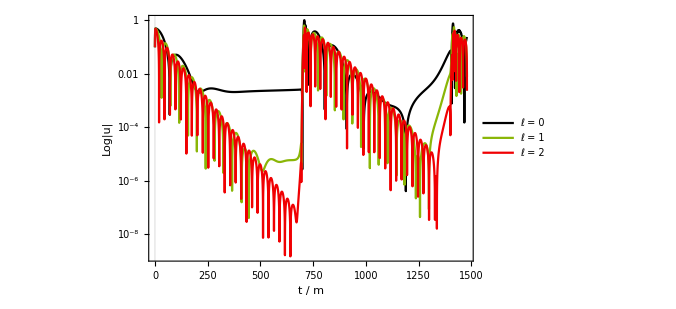

```mathematica
Block[{$RecursionLimit=Infinity,start=1},Show[ListLogPlot[{data0[[;;6000,;;]],data1[[;;6000,;;]],data2[[start;;6000,;;]]
},Joined->True,PlotRange->All,Frame->True,ImageSize->500,Background->White,PlotTheme->"Scientific",PlotLegends->Placed[{Style["ℓ = 0",15],Style["ℓ = 1",15],Style["ℓ = 2",15]},{Scaled[{0.78,0.67}], {0,0}}],PlotStyle->colorlist],FrameLabel-> {{RawBoxes[RowBox[{"Log|u|"}]],None},{"t / m",None}},
FrameStyle->Directive[Black,17],
PlotLabel->None,PlotRange->{{0,1350},{2,-21}},
LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15}]]
```

```mathematica
SetDirectory["C:\\Users\\tsits\\OneDrive\\Έγγραφα\\Wolfram Mathematica\\PhD-2\\Grav_Petrurbations_NMDC\\3rd Run-Plots\\"];
Export["GP_Rin_leta01manymasses.pdf",NotebookRead[PreviousCell[]]]
```

GP_Rin_leta01manymasses.pdf

## Graphs - a = 2 , lambda = 2 & w.r.t. leta = 5,10

```mathematica
SetDirectory["C:\\Users\\tsits\\OneDrive\\Έγγραφα\\Wolfram Mathematica\\PhD-2\\BhWhTransition\\Two_way_data\\"];
data0=Import["Two_way_leta2a2m0.1l2data.txt","Table"]//ToExpression;
data1=Import["Two_way_leta5a2m0.1l2data.txt","Table"]//ToExpression;
data2=Import["Two_way_leta10a2m0.1l2data.txt","Table"]//ToExpression;
```

```mathematica
null[_String]:=Null
Length@ReadList[#,null@String,NullRecords->True]&/@{"Two_way_leta2a2m0.1l2data.txt","Two_way_leta5a2m0.1l2data.txt","Two_way_leta10a2m0.1l2data.txt"}
```

{4001,5001,6001}

```mathematica
data0[[;;,2]]=Abs[data0[[;;,2]]];
data1[[;;,2]]=Abs[data1[[;;,2]]];
data2[[;;,2]]=Abs[data2[[;;,2]]];
```

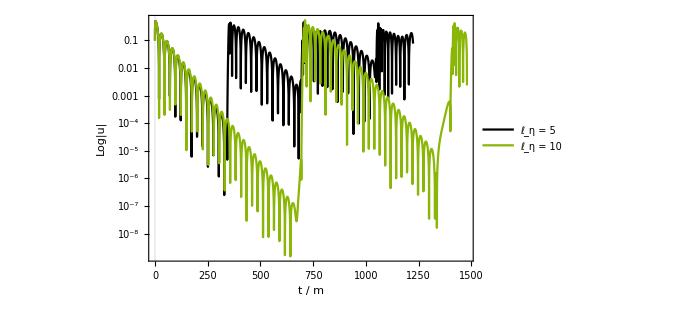

```mathematica
Block[{$RecursionLimit=Infinity,start=1},Show[ListLogPlot[{data1[[start;;5000,;;]],data2[[start;;6000,;;]]
},Joined->True,PlotRange->All,Frame->True,ImageSize->500,Background->White,PlotTheme->"Scientific",PlotLegends->Placed[{Style["ℓ_η = 5",15],Style["ℓ_η = 10",15]},{Scaled[{0.78,0.15}], {0,0}}],PlotStyle->colorlist],FrameLabel-> {{RawBoxes[RowBox[{"Log|u|"}]],None},{"t / m",None}},
FrameStyle->Directive[Black,17],
PlotLabel->None,PlotRange->{{0,1000},{2,-21}},
LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15}]]
```

```mathematica
Block[{ε=1,m=0.1,leta,η},
times=100;
V1=Plot[{Veff[r,2]/.leta->5},{r,-times,times},PlotRange->All,PlotTheme->"Scientific",PlotLegends->{Placed[{Style["ℓ_η = 5",15]},{0.798,0.7}]},PlotStyle->colorlist[[1]],Frame->True];
V2=Plot[{Veff[r,2]/.leta->10 },{r,-times,times},PlotRange->All,PlotTheme->"Scientific",PlotLegends->{Placed[{Style["ℓ_η = 10",15]},{0.8,0.62}]},PlotStyle->colorlist[[2]],Frame->True];
]
```

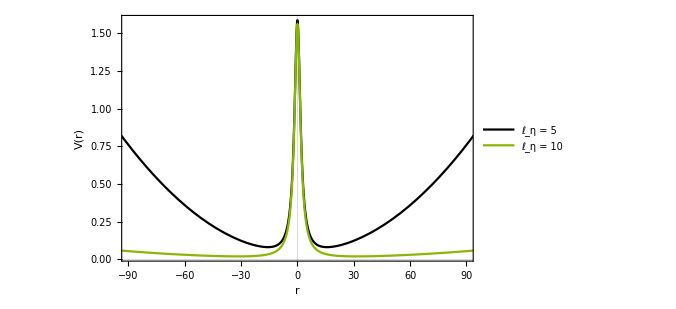

```mathematica
Show[{V1,V2},PlotRange->{{-90,90},All},ImageSize->500,
FrameLabel->{{HoldForm["V(r)" ],None},{HoldForm["r"],None}},
FrameStyle->Directive[Black,17],LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15},Background->White]
```

## Setup - leta = 5 , lambda = 2 & w.r.t. a = 1,2,3

### a = 1,2(ready),3 - lambda = 2

```mathematica
FDrin[xstarmin+10^-7,xstarmax-10^-7,1000,50,2]
```

leta = 5, m = 0.1, lambda = 2

Part::partw: Part 2 of {} does not exist.

r_horizon = {}⟦1,2,1,2⟧

Location of Gaussian's center = 0.01000000000000000020816681711721685132943093776702880859375

# of Iterations in space = 1000

(r_*)^max =  17.0021935705178684166505040957721781200210795118178448093037803477261989644855402778223882761959092  , r^max =  1.4999999999999999530×10^9

(r_*)^min =  -17.0206834808150175438150909764208313868546002686313923679205475105889635258609497638901874648250097  ,  r^min =  -1.4999999999999999530×10^9

I_max = 499

I_min = -500

Space Discretization step = 0.0340229

t_final/M = 500.

# of Iterations in time = J_max = 2099

Time Discretization step = 0.023816

Δt/(Δr_*) = 0.7

```mathematica
Clear[Viplot,OrigV,VrPlot]
Viplot = ListPlot[Table[{i Δrstar,V[i]},{i,imin,imax}],PlotStyle->Directive[Black,Thick],PlotRange->All];
OrigV = Plot[Veff[x[rstar],lambda],{rstar,imin*Δrstar,(imax-10)*Δrstar},PlotStyle->colorlist,PlotRange->All];
VrPlot=Plot[{Veff[r,2]},{r,horizonsol[leta,a],10*horizonsol[leta,a]},PlotRange->Automatic,PlotStyle->colorlist(*{{horizon,10*horizon},{0,100}}*),AxesOrigin->{0,0},PlotLegends->"Expressions"];
```

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Plot::plln: Limiting value {}⟦1,2,1,2⟧ in {r,{}⟦1,2,1,2⟧,10 {}⟦1,2,1,2⟧} is not a machine-sized real number.

```mathematica
Psiplot = Plot[PsiSquare[x[rstar]],{rstar,imin*Δrstar,imax*Δrstar},PlotStyle->colorlist[[2]],PlotRange->All];
Psirplot = Plot[PsiSquare[r],{r,horizonsol[leta,a],10*horizonsol[leta,a]},PlotStyle->colorlist[[2]],PlotRange->All];
```

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Plot::plln: Limiting value {}⟦1,2,1,2⟧ in {r,{}⟦1,2,1,2⟧,10 {}⟦1,2,1,2⟧} is not a machine-sized real number.

```mathematica
Row[{Show[{Viplot,OrigV},PlotRange->Automatic(*{{-10,5},{-0.5,0.5}}*),ImageSize->Small], Show[{VrPlot,Psirplot},ImageSize->Small]}]
```

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Plot::plln: Limiting value {}⟦1,2,1,2⟧ in {r,{}⟦1,2,1,2⟧,10 {}⟦1,2,1,2⟧} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[{Plot[{Veff[r,2]},{r,horizonsol[leta,a],10 horizonsol[leta,a]},PlotRange→Automatic,PlotStyle→colorlist,AxesOrigin→{0,0},PlotLegends→Expressions],Plot[PsiSquare[r],{r,horizonsol[leta,a],10 horizonsol[leta,a]},PlotStyle→colorlist⟦2⟧,PlotRange→All]},ImageSize→Small].

-Graphics-Show[{Plot[{Veff[r,2]},{r,horizonsol[leta,a],10 horizonsol[leta,a]},PlotRange→Automatic,PlotStyle→colorlist,AxesOrigin→{0,0},PlotLegends→Expressions],Plot[PsiSquare[r],{r,horizonsol[leta,a],10 horizonsol[leta,a]},PlotStyle→colorlist⟦2⟧,PlotRange→All]},ImageSize→Small]

0.010000000000000000208

General::munfl: 1.01986 1.99153302074181209560578973202942222584301696166963923340424634052172316950356077010292997244642×10^-311 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.49 1.99153302075273287971298978072367771611617067942547047362676220274832847402936521752589846000017×10^-311 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.01986 4.94147587413875137199155271445927395343862835668856773713558983951061966969069686218080571664024×10^-317 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

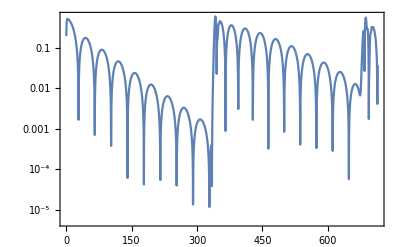

```mathematica
i=0;
(*lambda=5;*)
NumberForm[x[i*Δrstar],20]
Block[{$RecursionLimit=Infinity},ListLogPlot[{Table[{(j Δt)/m,Evaluate[Abs[ψ[i,j]]]},{j,3000}]  
(*,Table[{(j Δt)/M,Evaluate[10^3(j Δt)^(-(5))]},{j,1700,jmax}]*)},Joined->True,PlotRange->All,Frame->True] ]
```

```mathematica
Block[{$RecursionLimit=Infinity},ListPlot[{Table[{(j Δt)/m,Evaluate[ψ[i,j]]},{j,0,3000}]  
(*,Table[{(j Δt)/M,Evaluate[10^3(j Δt)^(-(5))]},{j,1700,jmax}]*)},Joined->True,PlotRange->{{20,100},{-0.01,0.01}}] ]
```

-Graphics-

```mathematica
data= Table[{(j Δt)/m ,ψ[i,j]},{j,0,3000}];
SetDirectory["C:\\Users\\tsits\\OneDrive\\Έγγραφα\\Wolfram Mathematica\\PhD-2\\BhWhTransition\\Two_way_data\\"];
(**)
Print["m = ",m," , α = ",a," , leta = ",leta," , lambda = ",lambda];
Export["Two_way_leta"<>ToString[leta]<>"a"<>ToString[a]<>"m"<>ToString[m]<>"l"<>ToString[lambda]<>"data.txt",data,"Table","FieldSeparators"->" "];
(**)
Print["File name :"]
Print["Two_way_leta"<>ToString[leta]<>"a"<>ToString[a]<>"m"<>ToString[m]<>"l"<>ToString[lambda]<>"data.txt"]
```

m = 0.1 , α = 3 , leta = 5 , lambda = 2

File name :

Two_way_leta5a3m0.1l2data.txt

### Final graphs ✓

```mathematica
SetDirectory["C:\\Users\\tsits\\OneDrive\\Έγγραφα\\Wolfram Mathematica\\PhD-2\\BhWhTransition\\Two_way_data\\"];
data0=Import["Two_way_leta5a1m0.1l2data.txt","Table"]//ToExpression;
data1=Import["Two_way_leta5a2m0.1l2data.txt","Table"]//ToExpression;
data2=Import["Two_way_leta5a3m0.1l2data.txt","Table"]//ToExpression;
```

Below command : to read the number of lines a txt file has

```mathematica
null[_String]:=Null
Length@ReadList[#,null@String,NullRecords->True]&/@{"Two_way_leta5a1m0.1l2data.txt","Two_way_leta5a2m0.1l2data.txt","Two_way_leta5a3m0.1l2data.txt"}
```

{3001,5001,3001}

```mathematica
data0[[;;,2]]=Abs[data0[[;;,2]]];
data1[[;;,2]]=Abs[data1[[;;,2]]];
data2[[;;,2]]=Abs[data2[[;;,2]]];
```

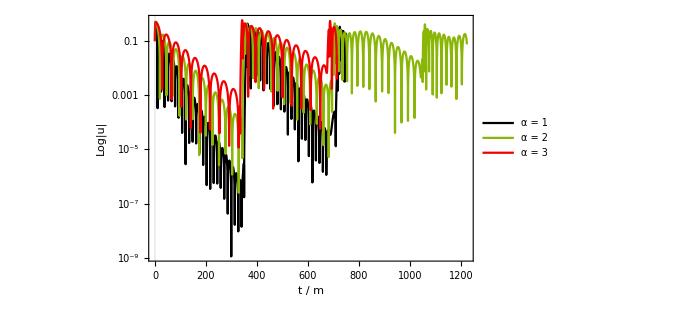

```mathematica
Block[{$RecursionLimit=Infinity,start=1},Show[ListLogPlot[{data0[[;;3000,;;]],data1[[;;5000,;;]],data2[[start;;3000,;;]]
},Joined->True,PlotRange->All,Frame->True,ImageSize->500,Background->White,PlotTheme->"Scientific",PlotLegends->Placed[{Style["α = 1",15],Style["α = 2",15],Style["α = 3",15]},{Scaled[{0.72,0.04}], {0,0}}],PlotStyle->colorlist],FrameLabel-> {{RawBoxes[RowBox[{"Log|u|"}]],None},{"t / m",None}},
FrameStyle->Directive[Black,17],
PlotLabel->None,PlotRange->{{0,650},{0,-21}},
LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15}]]
```

```mathematica
Block[{ε=1,m=0.1,leta=5,a},
times=100;
V1=Plot[{Veff[r,2]/.a->1},{r,-times,times},PlotRange->All,PlotTheme->"Scientific",PlotLegends->{Placed[{Style["α = 1",15]},{0.8,0.7}]},PlotStyle->colorlist[[1]],Frame->True];
V2=Plot[{Veff[r,2]/.a->2},{r,-times,times},PlotRange->All,PlotTheme->"Scientific",PlotLegends->{Placed[{Style["α = 2",15]},{0.8,0.62}]},PlotStyle->colorlist[[2]],Frame->True];
V3=Plot[{Veff[r,2]/.a->3 },{r,-times,times},PlotRange->All,PlotTheme->"Scientific",PlotLegends->{Placed[{Style["α = 3",15]},{0.8,0.54}]},PlotStyle->colorlist[[3]],Frame->True];
]
```

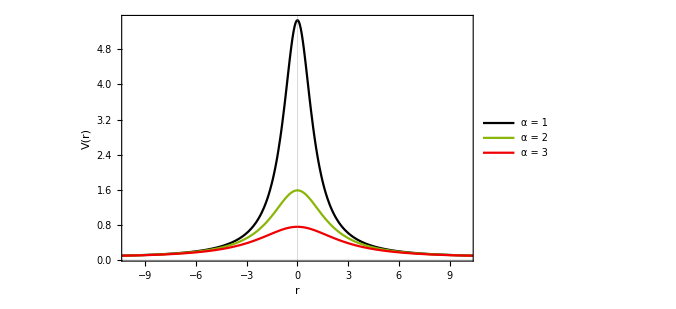

```mathematica
Show[{V1,V2,V3},PlotRange->{{-10,10},All},ImageSize->500,
FrameLabel->{{HoldForm["V(r)" ],None},{HoldForm["r"],None}},
FrameStyle->Directive[Black,17],LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15},Background->White]
```

```mathematica
SetDirectory["C:\\Users\\tsits\\OneDrive\\Έγγραφα\\Wolfram Mathematica\\PhD-2\\Grav_Petrurbations_NMDC\\3rd Run-Plots\\"];
Export["GP_Rin_leta01manymasses.pdf",NotebookRead[PreviousCell[]]]
```

GP_Rin_leta01manymasses.pdf

## Setup - leta = 5 , lambda = 2 & w.r.t. m = 0.1,0.2,0.3

### m = 0.1,0.2,0.3 - lambda = 2

```mathematica
FDrin[xstarmin+10^-7,xstarmax-10^-7,1000,50,2]
```

leta = 5, m = 0.4, lambda = 2

Part::partw: Part 2 of {} does not exist.

r_horizon = {}⟦1,2,1,2⟧

Location of Gaussian's center = 0.01000000000000000020816681711721685132943093776702880859375

# of Iterations in space = 1000

(r_*)^max =  21.9013258238328339036107080703004837333649644490274534722260797167904537613233769044462964455314581  , r^max =  1.4999999999999999547×10^9

(r_*)^min =  -21.9993580216686158473877523194578070133021238356351254356841299431409405505424124782874092017932543  ,  r^min =  -1.4999999999999999548×10^9

I_max = 498

I_min = -501

Space Discretization step = 0.0439007

t_final/M = 125.

# of Iterations in time = J_max = 1265

Time Discretization step = 0.0395106

Δt/(Δr_*) = 0.9

```mathematica
Clear[Viplot,OrigV,VrPlot]
Viplot = ListPlot[Table[{i Δrstar,V[i]},{i,imin,imax}],PlotStyle->Directive[Black,Thick],PlotRange->All];
OrigV = Plot[Veff[x[rstar],lambda],{rstar,imin*Δrstar,(imax-10)*Δrstar},PlotStyle->colorlist,PlotRange->All];
VrPlot=Plot[{Veff[r,2]},{r,horizonsol[leta,a],10*horizonsol[leta,a]},PlotRange->Automatic,PlotStyle->colorlist(*{{horizon,10*horizon},{0,100}}*),AxesOrigin->{0,0},PlotLegends->"Expressions"];
```

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Plot::plln: Limiting value {}⟦1,2,1,2⟧ in {r,{}⟦1,2,1,2⟧,10 {}⟦1,2,1,2⟧} is not a machine-sized real number.

```mathematica
Psiplot = Plot[PsiSquare[x[rstar]],{rstar,imin*Δrstar,imax*Δrstar},PlotStyle->colorlist[[2]],PlotRange->All];
Psirplot = Plot[PsiSquare[r],{r,horizonsol[leta,a],10*horizonsol[leta,a]},PlotStyle->colorlist[[2]],PlotRange->All];
```

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Plot::plln: Limiting value {}⟦1,2,1,2⟧ in {r,{}⟦1,2,1,2⟧,10 {}⟦1,2,1,2⟧} is not a machine-sized real number.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Plot::plln: Limiting value {}⟦1,2,1,2⟧ in {r,{}⟦1,2,1,2⟧,10 {}⟦1,2,1,2⟧} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[{Plot[{Veff[r,2]},{r,horizonsol[leta,a],10 horizonsol[leta,a]},PlotRange→Automatic,PlotStyle→colorlist,AxesOrigin→{0,0},PlotLegends→Expressions],Plot[PsiSquare[r],{r,horizonsol[leta,a],10 horizonsol[leta,a]},PlotStyle→colorlist⟦2⟧,PlotRange→All]},ImageSize→Small].

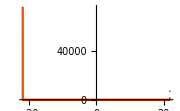
-Graphics-Show[{Plot[{Veff[r,2]},{r,horizonsol[leta,a],10 horizonsol[leta,a]},PlotRange→Automatic,PlotStyle→colorlist,AxesOrigin→{0,0},PlotLegends→Expressions],Plot[PsiSquare[r],{r,horizonsol[leta,a],10 horizonsol[leta,a]},PlotStyle→colorlist⟦2⟧,PlotRange→All]},ImageSize→Small]

```mathematica
Row[{Show[{Viplot,OrigV},PlotRange->Automatic(*{{-10,5},{-0.5,0.5}}*),ImageSize->Small], Show[{VrPlot,Psirplot},ImageSize->Small]}]
```

0.010000000000000000208

General::munfl: 0.377893 2.99491921701067189453771564989493277368416783204215329346550750468945260707183424118003048801262×10^-311 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.81 2.99491921701068007047138770214849430386180599423865108915223106323729711254301270430736430995883×10^-311 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.377912 1.72310353440819408495837506651368175085145913807091103152306844670843439396833590596126840221403×10^-318 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

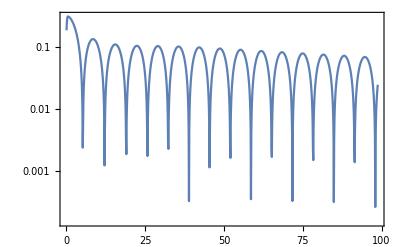

```mathematica
i=0;
(*lambda=5;*)
NumberForm[x[i*Δrstar],20]
Block[{$RecursionLimit=Infinity},ListLogPlot[{Table[{(j Δt)/m,Evaluate[Abs[ψ[i,j]]]},{j,1000}]  
(*,Table[{(j Δt)/M,Evaluate[10^3(j Δt)^(-(5))]},{j,1700,jmax}]*)},Joined->True,PlotRange->All,Frame->True] ]
```

```mathematica
Block[{$RecursionLimit=Infinity},ListPlot[{Table[{(j Δt)/m,Evaluate[ψ[i,j]]},{j,0,3000}]  
(*,Table[{(j Δt)/M,Evaluate[10^3(j Δt)^(-(5))]},{j,1700,jmax}]*)},Joined->True,PlotRange->{{20,100},{-0.01,0.01}}] ]
```

-Graphics-

```mathematica
data= Table[{(j Δt)/m ,ψ[i,j]},{j,0,6000}];
SetDirectory["C:\\Users\\tsits\\OneDrive\\Έγγραφα\\Wolfram Mathematica\\PhD-2\\BhWhTransition\\Two_way_data\\"];
(**)
Print["m = ",m," , α = ",a," , leta = ",leta," , lambda = ",lambda];
Export["Two_way_leta"<>ToString[leta]<>"a"<>ToString[a]<>"m"<>ToString[m]<>"l"<>ToString[lambda]<>"data.txt",data,"Table","FieldSeparators"->" "];
(**)
Print["File name :"]
Print["Two_way_leta"<>ToString[leta]<>"a"<>ToString[a]<>"m"<>ToString[m]<>"l"<>ToString[lambda]<>"data.txt"]
```

m = 0.4 , α = 1 , leta = 5 , lambda = 2

File name :

Two_way_leta5a1m0.4l2data.txt

### Final graphs ✓

```mathematica
SetDirectory["C:\\Users\\tsits\\OneDrive\\Έγγραφα\\Wolfram Mathematica\\PhD-2\\BhWhTransition\\Two_way_data\\"];
data0=Import["Two_way_leta5a1m0.1l2data.txt","Table"]//ToExpression;
data1=Import["Two_way_leta5a1m0.2l2data.txt","Table"]//ToExpression;
data2=Import["Two_way_leta5a1m0.3l2data.txt","Table"]//ToExpression;
(**)
data3=Import["Two_way_leta5a1m0.4l2data.txt","Table"]//ToExpression;
```

Below command : to read the number of lines a txt file has

```mathematica
null[_String]:=Null
Length@ReadList[#,null@String,NullRecords->True]&/@{"Two_way_leta5a1m0.1l2data.txt","Two_way_leta5a1m0.2l2data.txt","Two_way_leta5a1m0.3l2data.txt"}
```

{3001,5001,5001}

```mathematica
data0[[;;,2]]=Abs[data0[[;;,2]]];
data1[[;;,2]]=Abs[data1[[;;,2]]];
data2[[;;,2]]=Abs[data2[[;;,2]]];
data3[[;;,2]]=Abs[data3[[;;,2]]];
```

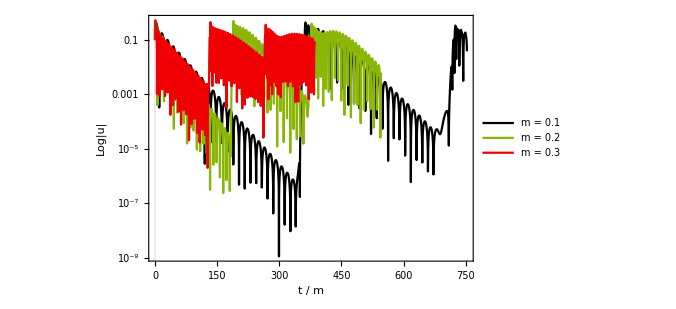

```mathematica
Block[{$RecursionLimit=Infinity,start=1},Show[ListLogPlot[{data0[[;;3000,;;]],data1[[;;5000,;;]],data2[[start;;5000,;;]]
},Joined->True,PlotRange->All,Frame->True,ImageSize->500,Background->White,PlotTheme->"Scientific",PlotLegends->Placed[{Style["m = 0.1",15],Style["m = 0.2",15],Style["m = 0.3",15]},{Scaled[{0.07,0.07}], {0,0}}],PlotStyle->colorlist],FrameLabel-> {{RawBoxes[RowBox[{"Log|u|"}]],None},{"t / m",None}},
FrameStyle->Directive[Black,17],
PlotLabel->None,PlotRange->{{0,250},{0,-21}},
LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15}]]
```

```mathematica
Block[{ε=1,a=1,leta=5,m,lam=10},
Clear[m];
times=200;
V1=Plot[{Veff[r,lam]/.m->0.1},{r,-times,times},PlotRange->All,PlotTheme->"Scientific",PlotLegends->{Placed[{Style["m = 0.1",15]},{0.8,0.7}]},PlotStyle->colorlist[[1]],Frame->True];
V2=Plot[{Veff[r,lam]/.m->0.2},{r,-times,times},PlotRange->All,PlotTheme->"Scientific",PlotLegends->{Placed[{Style["m = 0.2",15]},{0.8,0.62}]},PlotStyle->colorlist[[2]],Frame->True];
V3=Plot[{Veff[r,lam]/.m->0.3 },{r,-times,times},PlotRange->All,PlotTheme->"Scientific",PlotLegends->{Placed[{Style["m = 0.3",15]},{0.8,0.54}]},PlotStyle->colorlist[[3]],Frame->True];
V4=Plot[{Veff[r,lam]/.m->0.4},{r,-times,times},PlotRange->All,PlotTheme->"Scientific",PlotLegends->{Placed[{Style["m = 0.4",15]},{0.8,0.46}]},PlotStyle->colorlist[[4]],Frame->True];
V5=Plot[{Veff[r,lam]/.m->0.5 },{r,-times,times},PlotRange->All,PlotTheme->"Scientific",PlotLegends->{Placed[{Style["m = 0.5",15]},{0.8,0.38}]},PlotStyle->colorlist[[5]],Frame->True];
]
```

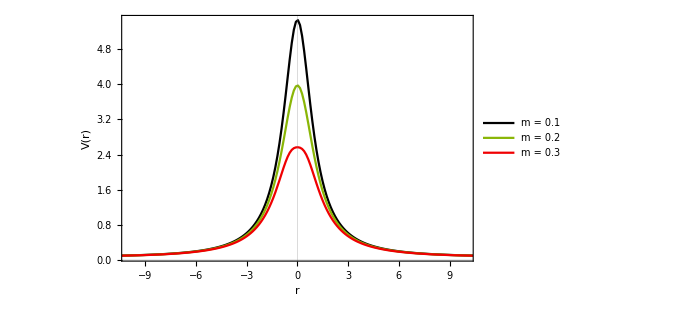

```mathematica
Show[{V1,V2,V3},PlotRange->{{-10,10},All},ImageSize->500,
FrameLabel->{{HoldForm["V(r)" ],None},{HoldForm["r"],None}},
FrameStyle->Directive[Black,17],LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15},Background->White]
```

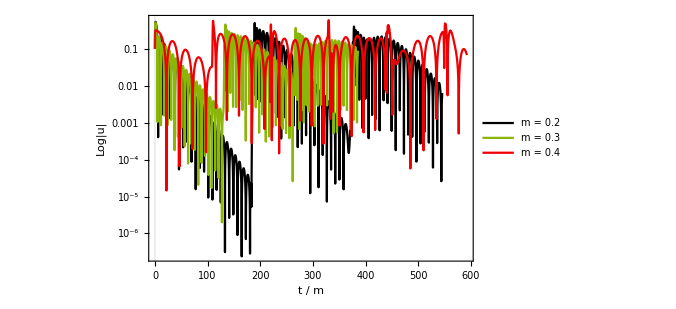

```mathematica
Block[{$RecursionLimit=Infinity,start=1},Show[ListLogPlot[{data1[[;;5000,;;]],data2[[start;;5000,;;]],data3[[start;;6000,;;]]
},Joined->True,PlotRange->All,Frame->True,ImageSize->500,Background->White,PlotTheme->"Scientific",PlotLegends->Placed[{Style["m = 0.2",15],Style["m = 0.3",15],Style["m = 0.4",15]},{Scaled[{0.07,0.07}], {0,0}}],PlotStyle->colorlist],FrameLabel-> {{RawBoxes[RowBox[{"Log|u|"}]],None},{"t / m",None}},
FrameStyle->Directive[Black,17],
PlotLabel->None,PlotRange->{{0,500},{0,-21}},
LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15}]]
```

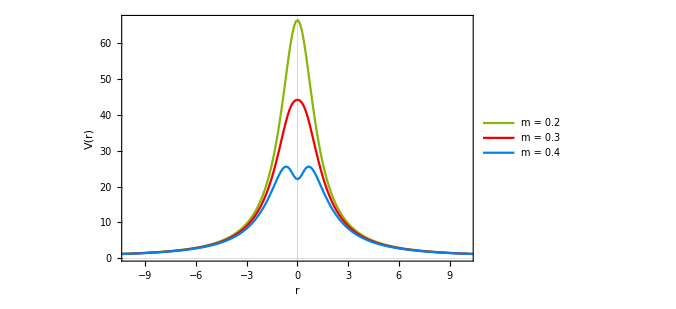

```mathematica
Show[{V2,V3,V4},PlotRange->{{-10,10},All},ImageSize->500,
FrameLabel->{{HoldForm["V(r)" ],None},{HoldForm["r"],None}},
FrameStyle->Directive[Black,17],LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15},Background->White]
```

```mathematica
SetDirectory["C:\\Users\\tsits\\OneDrive\\Έγγραφα\\Wolfram Mathematica\\PhD-2\\Grav_Petrurbations_NMDC\\3rd Run-Plots\\"];
Export["GP_Rin_leta01manymasses.pdf",NotebookRead[PreviousCell[]]]
```

GP_Rin_leta01manymasses.pdf

Part::partw: Part 2 of {} does not exist.

Horizon = {}⟦1,2,1,2⟧

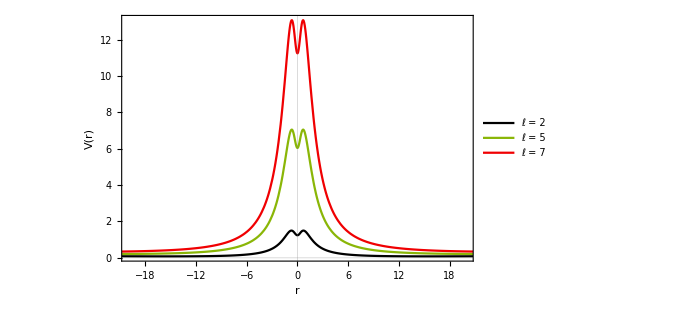

```mathematica
plotleta[5,1,{2,5,7},0.7,0.7]
Show[VstarPlot, PlotRange->{{-20,20},All},
FrameLabel->{{HoldForm["V(r)" ],None},{HoldForm["r"],None}},
FrameStyle->Directive[Black,17],LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15},Background->White]
```

## Setup - leta = 2 ,a =0.6 , m=0.3 ,l =0,1,2 ???

### lambda = 0, 1, 2

```mathematica
FDrin[xstarmin+10^-7,xstarmax-10^-7,2000,50,2]
```

leta = 2, m = 0.3, a = 0.6, lambda = 2

Part::partw: Part 2 of {} does not exist.

r_horizon = {}⟦1,2,1,2⟧

Location of Gaussian's center = 0.000010000000000000000818030539140313095458623138256371021270751953125

# of Iterations in space = 2000

(r_*)^max =  72.80020550167911337612531215984821348582585556751925576836874842519950000141502183298859323467001081  , r^max =  2.3999999999999995497×10^8

(r_*)^min =  -72.85057645103200074284087274276289404864069261848915416861532819114002922554309073748992608722936187  ,  r^min =  -2.3999999999999995495×10^8

I_max = 999

I_min = -1000

Space Discretization step = 0.0728254

t_final/M = 166.667

# of Iterations in time = J_max = 858

Time Discretization step = 0.0582603

Δt/(Δr_*) = 0.8

```mathematica
Clear[Viplot,OrigV,VrPlot]
Viplot = ListPlot[Table[{i Δrstar,V[i]},{i,imin,imax}],PlotStyle->Directive[Black,Thick],PlotRange->All];
OrigV = Plot[Veff[x[rstar],lambda],{rstar,imin*Δrstar,(imax-10)*Δrstar},PlotStyle->colorlist,PlotRange->All];
VrPlot=Plot[{Veff[r,2]},{r,horizonsol[leta,a],10*horizonsol[leta,a]},PlotRange->Automatic,PlotStyle->colorlist(*{{horizon,10*horizon},{0,100}}*),AxesOrigin->{0,0},PlotLegends->"Expressions"];
```

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Plot::plln: Limiting value {}⟦1,2,1,2⟧ in {r,{}⟦1,2,1,2⟧,10 {}⟦1,2,1,2⟧} is not a machine-sized real number.

```mathematica
Psiplot = Plot[PsiSquare[x[rstar]],{rstar,imin*Δrstar,imax*Δrstar},PlotStyle->colorlist[[2]],PlotRange->All];
Psirplot = Plot[PsiSquare[r],{r,horizonsol[leta,a],10*horizonsol[leta,a]},PlotStyle->colorlist[[2]],PlotRange->All];
```

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Plot::plln: Limiting value {}⟦1,2,1,2⟧ in {r,{}⟦1,2,1,2⟧,10 {}⟦1,2,1,2⟧} is not a machine-sized real number.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Plot::plln: Limiting value {}⟦1,2,1,2⟧ in {r,{}⟦1,2,1,2⟧,10 {}⟦1,2,1,2⟧} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[{Plot[{Veff[r,2]},{r,horizonsol[leta,a],10 horizonsol[leta,a]},PlotRange→Automatic,PlotStyle→colorlist,AxesOrigin→{0,0},PlotLegends→Expressions],Psirplot},ImageSize→Small].

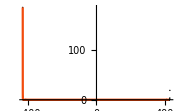
-Graphics-Show[{Plot[{Veff[r,2]},{r,horizonsol[leta,a],10 horizonsol[leta,a]},PlotRange→Automatic,PlotStyle→colorlist,AxesOrigin→{0,0},PlotLegends→Expressions],Psirplot},ImageSize→Small]

```mathematica
Row[{Show[{Viplot,OrigV},PlotRange->Automatic(*{{-10,5},{-0.5,0.5}}*),ImageSize->Small], Show[{VrPlot,Psirplot},ImageSize->Small]}]
```

0.000038915698738187396421

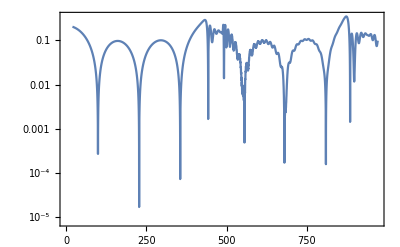

```mathematica
i=1;
(*lambda=5;*)
NumberForm[x[i*Δrstar],20]
Block[{$RecursionLimit=Infinity},ListLogPlot[{Table[{(j Δt)/m,Evaluate[Abs[ψ[i,j]]]},{j,100,5000}]  
(*,Table[{(j Δt)/M,Evaluate[10^3(j Δt)^(-(5))]},{j,1700,jmax}]*)},Joined->True,PlotRange->All,Frame->True] ]
```

```mathematica
Block[{$RecursionLimit=Infinity},ListPlot[{Table[{(j Δt)/m,Evaluate[ψ[i,j]]},{j,0,3000}]  
(*,Table[{(j Δt)/M,Evaluate[10^3(j Δt)^(-(5))]},{j,1700,jmax}]*)},Joined->True,PlotRange->{{20,100},{-0.01,0.01}}] ]
```

-Graphics-

```mathematica
data= Table[{(j Δt)/m ,ψ[i,j]},{j,0,6000}]  ;
SetDirectory["C:\\Users\\tsits\\OneDrive\\Έγγραφα\\Wolfram Mathematica\\PhD-2\\BhWhTransition\\Two_way_data\\"];
(**)
Print["m = ",m," , α = ",a," , leta = ",leta," , lambda = ",lambda];
Export["Two_way_leta"<>ToString[leta]<>"a"<>ToString[a]<>"m"<>ToString[m]<>"l"<>ToString[lambda]<>"data.txt",data,"Table","FieldSeparators"->" "];
(**)
Print["File name :"]
Print["Two_way_leta"<>ToString[leta]<>"a"<>ToString[a]<>"m"<>ToString[m]<>"l"<>ToString[lambda]<>"data.txt"]
```

m = 0.1 , α = 2 , leta = 10 , lambda = 2

File name :

Two_way_leta10a2m0.1l2data.txt

### Final graphs ✓???

```mathematica
SetDirectory["C:\\Users\\tsits\\OneDrive\\Έγγραφα\\Wolfram Mathematica\\PhD-2\\BhWhTransition\\Two_way_data\\"];
data0=Import["Two_way_leta10a2m0.1l0data.txt","Table"]//ToExpression;
data1=Import["Two_way_leta10a2m0.1l1data.txt","Table"]//ToExpression;
data2=Import["Two_way_leta10a2m0.1l2data.txt","Table"]//ToExpression;
```

Below command : to read the number of lines a txt file has

```mathematica
null[_String]:=Null
Length@ReadList[#,null@String,NullRecords->True]&/@{"Two_way_leta10a2m0.1l0data.txt","Two_way_leta10a2m0.1l1data.txt","Two_way_leta10a2m0.1l2data.txt"}
```

{6001,6001,6001}

```mathematica
data0[[;;,2]]=Abs[data0[[;;,2]]];
data1[[;;,2]]=Abs[data1[[;;,2]]];
data2[[;;,2]]=Abs[data2[[;;,2]]];
```

```mathematica
Block[{$RecursionLimit=Infinity,start=1},Show[ListLogPlot[{data0[[;;6000,;;]],data1[[;;6000,;;]],data2[[start;;6000,;;]]
},Joined->True,PlotRange->All,Frame->True,ImageSize->500,Background->White,PlotTheme->"Scientific",PlotLegends->Placed[{Style["ℓ = 0",15],Style["ℓ = 1",15],Style["ℓ = 2",15]},{Scaled[{0.78,0.67}], {0,0}}],PlotStyle->colorlist],FrameLabel-> {{RawBoxes[RowBox[{"Log|u|"}]],None},{"t / m",None}},
FrameStyle->Directive[Black,17],
PlotLabel->None,PlotRange->{{0,1350},{2,-21}},
LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15}]]
```

-Graphics-

Part::partw: Part 2 of {} does not exist.

Horizon = {}⟦1,2,1,2⟧

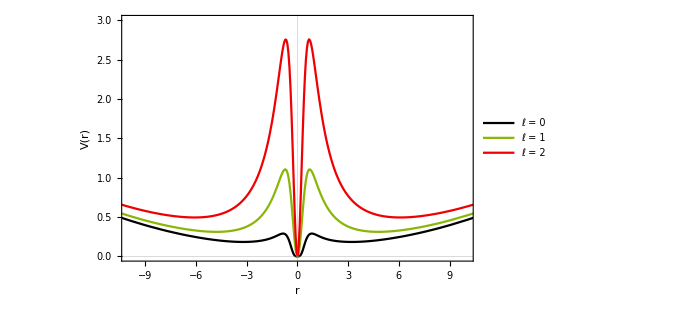

```mathematica
plotleta[2,0.6,{0,1,2},.7,.7];
Show[VstarPlot, PlotRange->{{-10,10},{0,3}},
FrameLabel->{{HoldForm["V(r)" ],None},{HoldForm["r"],None}},
FrameStyle->Directive[Black,17],LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15},Background->White]
```